```mathematica
Exit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/viktor/Documents/KerrSpinningFluxes

```mathematica
Get["/home/viktor/Documents/KerrSpinningFluxes/SpinningTrajectory.wl"]
```

```mathematica
Get["/home/viktor/Documents/KerrSpinningFluxes/TeukolskySpinFluxes.wl"]
```

## Fluxes

```mathematica
a=0.9`64
p=12.0`64
e=0.2`64
x=Cos[30Degree]
```

0.9

12.

0.2

(√3)/2

```mathematica
l=3
m=2
n=1
k=1
```

3

2

1

1

```mathematica
PacletDirectoryLoad["~/BHPT/SpinWeightedSpheroidalHarmonics-master"]
```

{/home/viktor/BHPT/SpinWeightedSpheroidalHarmonics-master}

```mathematica
<<Teukolsky`
```

```mathematica
corr=KerrSpinOrbitCorrection[a,p,e,x,12,12]
```

Calculating t, ϕ equations

Calculating r equation

Calculating θ equation

Calculating norm equation

Calculating submatrices

Calculating v

Calculating ES,LS

Calculating UtSlist, UϕSlist

Calculating Uthatlist, Uϕhatlist

Calculating UtSfour, UϕSfour

Calculating Uthatfour, Uϕhatfour

Calculating ImΔtSfour, ImΔϕSfour

<|a→0.9,p→12.,e→0.2,ℐ→π/6,Ehat→0.96169731977950340076094048662676575728187930428534883594488564,Lzhat→3.26946895953061732307367216562517597552783910348238119845524,Khat→9.35729204317729381252747992024611720194721966562266895078203,TrajectoryCorrection→{Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`ΔtS$5464[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`rS$5464[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`zS$5464[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`ΔϕS$5464[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]]},TrajectoryGeo→{Function[{qt$,qr$,qθ$},qt$+48.4227140110098950966206871860832918623014449279215115282529 (0.99973419140397440858142491472428743354468622905234933765388 (π/2+qθ$)-EllipticE[JacobiAmplitude[1.00026591462901463426185084574753284394941641014342173576272 (π/2+qθ$),0.00106302241207983298611420667663726857716172695882774291837689],0.00106302241207983298611420667663726857716172695882774291837689])-0.30400168717448545597298034820944021088860086165361909254514 (-39.2811726805751670079869497044560644017646524865638702540879 (-10.584583093513534185902202155245342639798682176968868409 (0.50610870976311586213003178008277715178696100537810427966 qr$-EllipticPi[0.00012816537837747754357373998453928846119256715014811576557,JacobiAmplitude[0.50607607945111040525744579822035252794083833548190581110258 qr$,0.047306880704356361897786730327765770172451556886329249391195],0.047306880704356361897786730327765770172451556886329249391195])+0.13200421028295365677409264899391916606753555444292509130181 (0.51500752397440667739138187263490482999599726898280753236584 qr$-EllipticPi[0.034180505642326746052015908471025362384770730301303087523748,JacobiAmplitude[0.50607607945111040525744579822035252794083833548190581110258 qr$,0.047306880704356361897786730327765770172451556886329249391195],0.047306880704356361897786730327765770172451556886329249391195]))+262.121316378718388843237443316339551098002081231863547759333 (0.6378238877579755925631473021786408600720993087767854574959 qr$-EllipticPi[0.368700753935232129038866542769629518459829481229837738406366,JacobiAmplitude[0.50607607945111040525744579822035252794083833548190581110258 qr$,0.047306880704356361897786730327765770172451556886329249391195],0.047306880704356361897786730327765770172451556886329249391195])+133.187559222230991033921590410008456080907832131171905552353 (0.49403312671222342966811902255771321028182679075582817205597 qr$-EllipticE[JacobiAmplitude[0.50607607945111040525744579822035252794083833548190581110258 qr$,0.047306880704356361897786730327765770172451556886329249391195],0.047306880704356361897786730327765770172451556886329249391195]+(0.368700753935232129038866542769629518459829481229837738406366 JacobiCN[0.50607607945111040525744579822035252794083833548190581110258 qr$,0.047306880704356361897786730327765770172451556886329249391195] JacobiSN[0.50607607945111040525744579822035252794083833548190581110258 qr$,0.047306880704356361897786730327765770172451556886329249391195] √(1-0.047306880704356361897786730327765770172451556886329249391195 JacobiSN[0.50607607945111040525744579822035252794083833548190581110258 qr$,0.047306880704356361897786730327765770172451556886329249391195]^2))/(1-0.368700753935232129038866542769629518459829481229837738406366 JacobiSN[0.50607607945111040525744579822035252794083833548190581110258 qr$,0.047306880704356361897786730327765770172451556886329249391195]^2))),Listable],Function[{qr$},(-135.611331049198931636201827401962028890370749668574863217365+7.1943344754005341818990862990189855548146251657125683913174 JacobiSN[0.50607607945111040525744579822035252794083833548190581110258 qr$,0.047306880704356361897786730327765770172451556886329249391195]^2)/(-13.5611331049198931636201827401962028890370749668574863217365+5. JacobiSN[0.50607607945111040525744579822035252794083833548190581110258 qr$,0.047306880704356361897786730327765770172451556886329249391195]^2),Listable],Function[{qθ$},ArcCos[1/2 JacobiSN[1.00026591462901463426185084574753284394941641014342173576272 (π/2+qθ$),0.00106302241207983298611420667663726857716172695882774291837689]],Listable],Function[{qϕ$,qr$,qθ$},qϕ$+0.627684931449211728647445107943046556755424335426409059498479 (-63.107920098857995343885874238284142776138690050155845812 (0.50610870976311586213003178008277715178696100537810427966 qr$-EllipticPi[0.00012816537837747754357373998453928846119256715014811576557,JacobiAmplitude[0.50607607945111040525744579822035252794083833548190581110258 qr$,0.047306880704356361897786730327765770172451556886329249391195],0.047306880704356361897786730327765770172451556886329249391195])+2.0033422612562087738342297957354788104167813718438132423602 (0.51500752397440667739138187263490482999599726898280753236584 qr$-EllipticPi[0.034180505642326746052015908471025362384770730301303087523748,JacobiAmplitude[0.50607607945111040525744579822035252794083833548190581110258 qr$,0.047306880704356361897786730327765770172451556886329249391195],0.047306880704356361897786730327765770172451556886329249391195]))-0.864182233538598328109558126571480301815050454723142400448823 (1.15502964018137534306284234178360064749281584054615177907315 (π/2+qθ$)-EllipticPi[1/4,JacobiAmplitude[1.00026591462901463426185084574753284394941641014342173576272 (π/2+qθ$),0.00106302241207983298611420667663726857716172695882774291837689],0.00106302241207983298611420667663726857716172695882774291837689]),Listable]},MinoFrequenciesGeo→{174.40311720101345332028293726927914238404826220621788518,3.1254791493815159933358554719973746613824943949147145423774,3.78230385233185625394540148384629020116913018742704727362325,3.92570863559516265200867805466087601497447889442614658},BLFrequenciesGeo→{0.017921005080311453809464401260483808347952603180714130498,0.021687134456274944124239925846286517663370740855613811604,0.0225093948926983423838545537710686971589824568437305018},FourVelocityCorrection→{Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`udtS$5464[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},(12. 0.2 (SpinningOrbit`Private`χrhat$5464'[SpinningOrbit`Private`wr$] (Cos[SpinningOrbit`Private`χrhat$5464[SpinningOrbit`Private`wr$]] SpinningOrbit`Private`δχrS$5464[SpinningOrbit`Private`wr$] SpinningOrbit`Private`Υrhat$5464+Sin[SpinningOrbit`Private`χrhat$5464[SpinningOrbit`Private`wr$]] SpinningOrbit`Private`ΥrS$5464+(2 0.2 Sin[SpinningOrbit`Private`χrhat$5464[SpinningOrbit`Private`wr$]]^2 SpinningOrbit`Private`δχrS$5464[SpinningOrbit`Private`wr$] SpinningOrbit`Private`Υrhat$5464)/(1+0.2 Cos[SpinningOrbit`Private`χrhat$5464[SpinningOrbit`Private`wr$]]))+Sin[SpinningOrbit`Private`χrhat$5464[SpinningOrbit`Private`wr$]] SpinningOrbit`Private`dδχrS$5464[SpinningOrbit`Private`wr$]))/(1+0.2 Cos[SpinningOrbit`Private`χrhat$5464[SpinningOrbit`Private`wr$]])^2+SpinningOrbit`Private`dδ𝔯$5464[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},-Sin[SpinningOrbit`Private`ℐ$5464] (SpinningOrbit`Private`χθhat$5464'[SpinningOrbit`Private`wz$] (Cos[SpinningOrbit`Private`χθhat$5464[SpinningOrbit`Private`wz$]] SpinningOrbit`Private`δχθS$5464[SpinningOrbit`Private`wz$] SpinningOrbit`Private`Υθhat$5464+Sin[SpinningOrbit`Private`χθhat$5464[SpinningOrbit`Private`wz$]] SpinningOrbit`Private`ΥθS$5464)+Sin[SpinningOrbit`Private`χθhat$5464[SpinningOrbit`Private`wz$]] SpinningOrbit`Private`dδχθS$5464[SpinningOrbit`Private`wz$])+SpinningOrbit`Private`dδ𝔷$5464[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`udϕS$5464[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]]},Spin4vector→{Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`St$5464[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`Sr$5464[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`Sz$5464[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`Sϕ$5464[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]]},TrajectoryDeltas→<|Δtr→Function[{qr$},-0.30400168717448545597298034820944021088860086165361909254514 (-39.2811726805751670079869497044560644017646524865638702540879 (-10.584583093513534185902202155245342639798682176968868409 (0.50610870976311586213003178008277715178696100537810427966 qr$-EllipticPi[0.00012816537837747754357373998453928846119256715014811576557,JacobiAmplitude[0.50607607945111040525744579822035252794083833548190581110258 qr$,0.047306880704356361897786730327765770172451556886329249391195],0.047306880704356361897786730327765770172451556886329249391195])+0.13200421028295365677409264899391916606753555444292509130181 (0.51500752397440667739138187263490482999599726898280753236584 qr$-EllipticPi[0.034180505642326746052015908471025362384770730301303087523748,JacobiAmplitude[0.50607607945111040525744579822035252794083833548190581110258 qr$,0.047306880704356361897786730327765770172451556886329249391195],0.047306880704356361897786730327765770172451556886329249391195]))+262.121316378718388843237443316339551098002081231863547759333 (0.6378238877579755925631473021786408600720993087767854574959 qr$-EllipticPi[0.368700753935232129038866542769629518459829481229837738406366,JacobiAmplitude[0.50607607945111040525744579822035252794083833548190581110258 qr$,0.047306880704356361897786730327765770172451556886329249391195],0.047306880704356361897786730327765770172451556886329249391195])+133.187559222230991033921590410008456080907832131171905552353 (0.49403312671222342966811902255771321028182679075582817205597 qr$-EllipticE[JacobiAmplitude[0.50607607945111040525744579822035252794083833548190581110258 qr$,0.047306880704356361897786730327765770172451556886329249391195],0.047306880704356361897786730327765770172451556886329249391195]+(0.368700753935232129038866542769629518459829481229837738406366 JacobiCN[0.50607607945111040525744579822035252794083833548190581110258 qr$,0.047306880704356361897786730327765770172451556886329249391195] JacobiSN[0.50607607945111040525744579822035252794083833548190581110258 qr$,0.047306880704356361897786730327765770172451556886329249391195] √(1-0.047306880704356361897786730327765770172451556886329249391195 JacobiSN[0.50607607945111040525744579822035252794083833548190581110258 qr$,0.047306880704356361897786730327765770172451556886329249391195]^2))/(1-0.368700753935232129038866542769629518459829481229837738406366 JacobiSN[0.50607607945111040525744579822035252794083833548190581110258 qr$,0.047306880704356361897786730327765770172451556886329249391195]^2))),Listable],Δtθ→Function[{qθ$},48.4227140110098950966206871860832918623014449279215115282529 (0.99973419140397440858142491472428743354468622905234933765388 (π/2+qθ$)-EllipticE[JacobiAmplitude[1.00026591462901463426185084574753284394941641014342173576272 (π/2+qθ$),0.00106302241207983298611420667663726857716172695882774291837689],0.00106302241207983298611420667663726857716172695882774291837689]),Listable],Δϕr→Function[{qr$},0.627684931449211728647445107943046556755424335426409059498479 (-63.107920098857995343885874238284142776138690050155845812 (0.50610870976311586213003178008277715178696100537810427966 qr$-EllipticPi[0.00012816537837747754357373998453928846119256715014811576557,JacobiAmplitude[0.50607607945111040525744579822035252794083833548190581110258 qr$,0.047306880704356361897786730327765770172451556886329249391195],0.047306880704356361897786730327765770172451556886329249391195])+2.0033422612562087738342297957354788104167813718438132423602 (0.51500752397440667739138187263490482999599726898280753236584 qr$-EllipticPi[0.034180505642326746052015908471025362384770730301303087523748,JacobiAmplitude[0.50607607945111040525744579822035252794083833548190581110258 qr$,0.047306880704356361897786730327765770172451556886329249391195],0.047306880704356361897786730327765770172451556886329249391195])),Listable],Δϕθ→Function[{qθ$},-0.864182233538598328109558126571480301815050454723142400448823 (1.15502964018137534306284234178360064749281584054615177907315 (π/2+qθ$)-EllipticPi[1/4,JacobiAmplitude[1.00026591462901463426185084574753284394941641014342173576272 (π/2+qθ$),0.00106302241207983298611420667663726857716172695882774291837689],0.00106302241207983298611420667663726857716172695882774291837689]),Listable]|>,MinoFrequenciesCorrection→{-0.2465265997804662847,0.1278863291755165139,-0.0579672427314624072,-0.1252293888921873711},BLFrequenciesCorrection→{0.0007586122068570764093,-0.0003017193044452612303,-0.0006862275527348154267},ES→-0.0009282141816583020484,LS→0.64524397688509669674,δχrS→SpinningOrbit`Private`δχrS$5464,δχθS→SpinningOrbit`Private`δχθS$5464,δr→SpinningOrbit`Private`δ𝔯$5464,δz→SpinningOrbit`Private`δ𝔷$5464,OrbitCorrection→Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`OrbitCorrection$5464[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],error→0.|>

```mathematica
corr["error"]
```

0.

```mathematica
modes0=Table[TeukolskySpinModeFromCorrection[l,m,n,k,corr,s*0.01`64],{s,{-1,-1/2,1/2,1}}]
```

64 steps in wr, 32 steps in wθ

64 steps in wr, 32 steps in wθ

64 steps in wr, 32 steps in wθ

«1 more identical outputs»

{<|l→3,m→2,k→1,n→1,ω→0.084636084944013660858157,Amplitudes→<|ℐ→-0.000043188487159889439-0.000093804948606120308 ⅈ,ℋ→0.000013839746366341432+0.0000270341296688393283 ⅈ|>,α→-0.0001546615122548318873005,S→-0.3722626966287886737,Fluxes→<|Energy→<|ℐ→1.1847429623364339×10^-7,ℋ→-1.5847925737860715×10^-12|>,AngularMomentum→<|ℐ→2.7996166484310689×10^-6,ℋ→-3.744957188968284×10^-11|>|>,stepsr→64,stepsθ→32|>,<|l→3,m→2,k→1,n→1,ω→0.084631507132998371779785,Amplitudes→<|ℐ→-0.000043169116667171811-0.0000937662059027737258 ⅈ,ℋ→0.0000138391052037757026+0.0000270328874147307411 ⅈ|>,α→-0.0001546412775634484038999,S→-0.3722627527739629308,Fluxes→<|Energy→<|ℐ→1.1838778945115479×10^-7,ℋ→-1.58461077292708915×10^-12|>,AngularMomentum→<|ℐ→2.7977237665189736×10^-6,ℋ→-3.74473012854863638×10^-11|>|>,stepsr→64,stepsθ→32|>,<|l→3,m→2,k→1,n→1,ω→0.084622351510967793623041,Amplitudes→<|ℐ→-0.000043130389615492814-0.0000936887392301169462 ⅈ,ℋ→0.0000138378158659040445+0.0000270303931038112972 ⅈ|>,α→-0.0001546008119403647311643,S→-0.3722628650621218019,Fluxes→<|Energy→<|ℐ→1.1821489511080657×10^-7,ℋ→-1.58424595469182897×10^-12|>,AngularMomentum→<|ℐ→2.7939402061046458×10^-6,ℋ→-3.74427305884189924×10^-11|>|>,stepsr→64,stepsθ→32|>,<|l→3,m→2,k→1,n→1,ω→0.084617773699952504544669,Amplitudes→<|ℐ→-0.000043111033056890191-0.000093650015266810779 ⅈ,ℋ→0.000013837167691137557+0.0000270291410465324087 ⅈ|>,α→-0.0001545805810087734942199,S→-0.3722629212051064167,Fluxes→<|Energy→<|ℐ→1.1812850755037516×10^-7,ℋ→-1.5840629374702702×10^-12|>,AngularMomentum→<|ℐ→2.7920495277800358×10^-6,ℋ→-3.7440430496014323×10^-11|>|>,stepsr→64,stepsθ→32|>}

```mathematica
modesNew=Table[TeukolskySpinModeFromCorrectionNew[l,m,n,k,corr,s*0.01`64],{s,{-1,-1/2,1/2,1}}]
```

64 steps in wr, 32 steps in wθ

64 steps in wr, 32 steps in wθ

64 steps in wr, 32 steps in wθ

«1 more identical outputs»

{<|l→3,m→2,k→1,n→1,ω→0.084636084944013660858157,Amplitudes→<|ℐ→-0.00004318848716810038-0.000093804948896424387 ⅈ,ℋ→0.0000138397462428403745+0.00002703412957257414 ⅈ|>,α→-0.0001546615122548318873005,S→-0.3722626966287886737,Fluxes→<|Energy→<|ℐ→1.1847429684656766×10^-7,ℋ→-1.5847925589698776×10^-12|>,AngularMomentum→<|ℐ→2.7996166629148266×10^-6,ℋ→-3.7449571539567545×10^-11|>|>,stepsr→64,stepsθ→32|>,<|l→3,m→2,k→1,n→1,ω→0.084631507132998371779785,Amplitudes→<|ℐ→-0.000043169116669222189-0.0000937662059752886092 ⅈ,ℋ→0.0000138391051728908706+0.0000270328873906531341 ⅈ|>,α→-0.0001546412775634484038999,S→-0.3722627527739629308,Fluxes→<|Energy→<|ℐ→1.1838778960420943×10^-7,ℋ→-1.58461076922178978×10^-12|>,AngularMomentum→<|ℐ→2.7977237701359396×10^-6,ℋ→-3.74473011979232448×10^-11|>|>,stepsr→64,stepsθ→32|>,<|l→3,m→2,k→1,n→1,ω→0.084622351510967793623041,Amplitudes→<|ℐ→-0.000043130389617538474-0.0000936887393025096481 ⅈ,ℋ→0.0000138378158350000801+0.0000270303930797110692 ⅈ|>,α→-0.0001546008119403647311643,S→-0.3722628650621218019,Fluxes→<|Energy→<|ℐ→1.1821489526350878×10^-7,ℋ→-1.58424595098403005×10^-12|>,AngularMomentum→<|ℐ→2.7939402097136736×10^-6,ℋ→-3.7442730500787324×10^-11|>|>,stepsr→64,stepsθ→32|>,<|l→3,m→2,k→1,n→1,ω→0.084617773699952504544669,Amplitudes→<|ℐ→-0.000043111033065063394-0.000093650015556137405 ⅈ,ℋ→0.0000138371675674834396+0.0000270291409500862517 ⅈ|>,α→-0.0001545805810087734942199,S→-0.3722629212051064167,Fluxes→<|Energy→<|ℐ→1.1812850816047998×10^-7,ℋ→-1.5840629226340799×10^-12|>,AngularMomentum→<|ℐ→2.792049542200288×10^-6,ℋ→-3.7440430145350633×10^-11|>|>,stepsr→64,stepsθ→32|>}

```mathematica
Table[modes0[[i]]["Amplitudes"]["ℐ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/(0.005`64)
```

3.8727051738788×10^-6+7.7466673657451×10^-6 ⅈ

```mathematica
δCI0=Table[modesNew[[i]]["Amplitudes"]["ℐ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/(0.005`64)
```

3.8727051738788×10^-6+7.7466673657451×10^-6 ⅈ

```mathematica
1-%/%%
```

0.+0. ⅈ

```mathematica
%/0.005`48^4
```

0.+0. ⅈ

```mathematica
Table[modes0[[i]]["Amplitudes"]["ℋ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/(0.005`64)
```

-1.289337961565×10^-7-2.4943108414385×10^-7 ⅈ

```mathematica
δCH0=Table[modesNew[[i]]["Amplitudes"]["ℋ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/(0.005`64)
```

-1.289337961565×10^-7-2.4943108414385×10^-7 ⅈ

```mathematica
1-%/%%
```

0.+0. ⅈ

```mathematica
%/0.005`48^4
```

0.+0. ⅈ

```mathematica
listspar={8,4,2,1,1/2,1/4,1/8,1/16}*0.01`64
```

{0.08,0.04,0.02,0.01,0.005,0.0025,0.00125,0.000625}

```mathematica
modesOldpex=Table[TeukolskySpinModeFromCorrectionNew[l,m,n,k,corr,listspar[[i]]],{i,1,Length[listspar]}]
```

64 steps in wr, 32 steps in wθ

64 steps in wr, 32 steps in wθ

64 steps in wr, 32 steps in wθ

«5 more identical outputs»

{<|l→3,m→2,k→1,n→1,ω→0.08455368434573845744746,Amplitudes→<|ℐ→-0.0000428405284382719-0.00009310855378711269 ⅈ,ℋ→0.000013827840049813475+0.000027011262764351351 ⅈ|>,α→-0.000154297479595431684664,S→-0.372263707130253738,Fluxes→<|Energy→<|ℐ→1.16923286404539×10^-7,ℋ→-1.5814572216079669×10^-12|>,AngularMomentum→<|ℐ→2.765657991352377×10^-6,ℋ→-3.7407174716158256×10^-11|>|>,stepsr→64,stepsθ→32|>,<|l→3,m→2,k→1,n→1,ω→0.08459030683386077007444,Amplitudes→<|ℐ→-0.00004299499116993944-0.000093417807015173965 ⅈ,ℋ→0.000013833227596006098+0.00002702155851500971 ⅈ|>,α→-0.000154459221741965300973,S→-0.372263258047686631,Fluxes→<|Energy→<|ℐ→1.176110251116208×10^-7,ℋ→-1.5829560877258832×10^-12|>,AngularMomentum→<|ℐ→2.780721090008912×10^-6,ℋ→-3.7426417918896579×10^-11|>|>,stepsr→64,stepsθ→32|>,<|l→3,m→2,k→1,n→1,ω→0.08460861807792192638793,Amplitudes→<|ℐ→-0.000043072333867991689-0.000093572587156641079 ⅈ,ℋ→0.000013835863836418075+0.0000270266267409876872 ⅈ|>,α→-0.0001545401229057645447393,S→-0.3722630334888860058,Fluxes→<|Energy→<|ℐ→1.179558538313323×10^-7,ℋ→-1.5836956278220366×10^-12|>,AngularMomentum→<|ℐ→2.7882704270786837×10^-6,ℋ→-3.7435799420893549×10^-11|>|>,stepsr→64,stepsθ→32|>,<|l→3,m→2,k→1,n→1,ω→0.084617773699952504544669,Amplitudes→<|ℐ→-0.000043111033065063394-0.000093650015556137405 ⅈ,ℋ→0.0000138371675674834396+0.0000270291409500862517 ⅈ|>,α→-0.0001545805810087734942199,S→-0.3722629212051064167,Fluxes→<|Energy→<|ℐ→1.1812850816047998×10^-7,ℋ→-1.5840629226340799×10^-12|>,AngularMomentum→<|ℐ→2.792049542200288×10^-6,ℋ→-3.7440430145350633×10^-11|>|>,stepsr→64,stepsθ→32|>,<|l→3,m→2,k→1,n→1,ω→0.084622351510967793623041,Amplitudes→<|ℐ→-0.000043130389617538474-0.0000936887393025096481 ⅈ,ℋ→0.0000138378158350000801+0.0000270303930797110692 ⅈ|>,α→-0.0001546008119403647311643,S→-0.3722628650621218019,Fluxes→<|Energy→<|ℐ→1.1821489526350878×10^-7,ℋ→-1.58424595098403005×10^-12|>,AngularMomentum→<|ℐ→2.7939402097136736×10^-6,ℋ→-3.7442730500787324×10^-11|>|>,stepsr→64,stepsθ→32|>,<|l→3,m→2,k→1,n→1,ω→0.084624640416475438162227,Amplitudes→<|ℐ→-0.0000431400696378703894-0.0000937081035768031674 ⅈ,ℋ→0.0000138381390691529175+0.0000270310179009291832 ⅈ|>,α→-0.0001546109278761582129132,S→-0.3722628369903557894,Fluxes→<|Energy→<|ℐ→1.18258103838579896×10^-7,ℋ→-1.58433731036430945×10^-12|>,AngularMomentum→<|ℐ→2.79488582182634389×10^-6,ℋ→-3.74438769267929986×10^-11|>|>,stepsr→64,stepsθ→32|>,<|l→3,m→2,k→1,n→1,ω→0.0846257848692292604318204,Amplitudes→<|ℐ→-0.000043144910072251343-0.0000937177862993370328 ⅈ,ℋ→0.0000138383004613240145+0.00002703133000064982468 ⅈ|>,α→-0.00015461598596155144081867,S→-0.37226282295440435686,Fluxes→<|Energy→<|ℐ→1.18279711840108887×10^-7,ℋ→-1.5843829513517199×10^-12|>,AngularMomentum→<|ℐ→2.79535869647494434×10^-6,ℋ→-3.74444492018606163×10^-11|>|>,stepsr→64,stepsθ→32|>,<|l→3,m→2,k→1,n→1,ω→0.0846263570956061715666169,Amplitudes→<|ℐ→-0.0000431473304053599906-0.00009372262781199633825 ⅈ,ℋ→0.00001383838110117892622+0.00002703148597279513554 ⅈ|>,α→-0.00015461851503362180415696,S→-0.372262815936411534,Fluxes→<|Energy→<|ℐ→1.18290516789391489×10^-7,ℋ→-1.584405762169596157×10^-12|>,AngularMomentum→<|ℐ→2.79559515141963193×10^-6,ℋ→-3.744473510491825314×10^-11|>|>,stepsr→64,stepsθ→32|>}

```mathematica
r1=p/(1-e)
r2=p/(1+e)
z1=Sqrt[1-x^2]
```

15.

10.

1/2

```mathematica
r1S=14.82194059906608056193273398763418391241032712357072524225634175563136817989492`59.26267647183203;r2S=-14.21141889319576563189809355464959997292452893838422882050597695470562236382046`59.29889914959862;
z1S=0.00675302307993867879497385742600893565562838762604497938784410322208171244797`56.87055034254505;
```

```mathematica
r1S=14.31694709123555135947477655371041825219114659880200772423262014474960023381754`59.35255265950888;
r2S=-13.71376714822918323664519898561833914073626963775378835342095955927479228063422`59.39280032062916;
z1S=0.03782695048030583946307486320723456073264693832258576348471349193009125316508`57.78314267359129;
```

```mathematica
orbitspex=Table[KerrSpinOrbit[a,2*(r1-spar*r1S)*(r2-spar*r2S)/((r1-spar*r1S)+(r2-spar*r2S)),((r1-spar*r1S)-(r2-spar*r2S))/((r1-spar*r1S)+(r2-spar*r2S)),Sqrt[1-(z1-spar*z1S)^2],spar],{spar,{-1,-1/2,1/2,1}*0.01`64}]
```

{<|a→0.9,p→11.9455175380865505937225105624158773477472083646869640339111,e→0.211161338382165692592042430496209474423902550302875712914335,x→0.8658068996071691490908857904805721379307912828645470881122633,spar→-0.01,Energy→0.96170660581653904632422706270888057522694910539605386849212,AngularMomentum→3.26284532859297946152046358237299902090461855057442739011,CarterConstantK→9.31821270996440392710132109157769096143286519218131233011,EnTilde→0.96158356148502338509290378811475205037547510654941324106171,JzTilde→3.26503675715452837163806851991121867026269965964020107236,KTilde→9.3263653403574990029819835207556960660175025844116587896,Frequencies→<|Υ_r→3.119166103682658537987148754466988096652706281467299,Υ_z→3.7769727642666260282038929872989001861608509723960442,Υ_ϕ→3.920885196716836050147770518364213887737778253764,Υ_t→174.12273356867716087115245662363881343569049362139|>,BLFrequencies→{0.017913606338212022806977501198637882699507391374651,0.021691439634887879467340234360745990576305760363377,0.02251793959558053854039221238935372806475278329833},TrajectoryDeltas→<|Δtr→Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`orbitTilde$28058[TrajectoryDeltas][Δtr][SpinningOrbit`Private`qr$]-(3 (-0.01) SpinningOrbit`Private`τTilde$28058[ProperTime][0,SpinningOrbit`Private`qr$,0])/(2 SpinningOrbit`Private`sqrtK$28058)],Δtz→Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`orbitTilde$28058[TrajectoryDeltas][Δtθ][SpinningOrbit`Private`qz$]-(3 (-0.01) SpinningOrbit`Private`τTilde$28058[ProperTime][0,0,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$28058)],Δϕr→Function[{qr$},0.628831331701982253265755404405697273787203895734473777 (-64.178282968669109433982393703694218996849087943362 (0.50614743706807672800536677052058134125066829077807 qr$-EllipticPi[0.00012427249181355586274275901291216955652052152000057,JacobiAmplitude[0.5061157942351368558849206185466534962895709592452613 qr$,0.047607703826431805042988447073103152872211419812958359],0.047607703826431805042988447073103152872211419812958359])+1.9987198995020082516839033674810142342748303426004733 (0.5151085012845384074674159231455894238149068799170719 qr$-EllipticPi[0.034404902698877207869284163511935715832630048258217768,JacobiAmplitude[0.5061157942351368558849206185466534962895709592452613 qr$,0.047607703826431805042988447073103152872211419812958359],0.047607703826431805042988447073103152872211419812958359])),Listable],Δϕz→Function[{qθ$},-0.86418721415467114198076516060483342578437910357006063 (1.1550106534640776418360147274527958496715847135759184 (π/2+qθ$)-EllipticPi[0.2499729321182360328890215887359637363908914802584256110626,JacobiAmplitude[1.0002674161386376153823896959247641995093429647137444 (π/2+qθ$),0.00106902124832256334099922411928704559613879810854974844],0.00106902124832256334099922411928704559613879810854974844]),Listable]|>,Trajectoryg→{Function[{SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},SpinningOrbit`Private`orbitTilde$28058[Trajectory]⟦1⟧[SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]-(3 (-0.01) SpinningOrbit`Private`τTilde$28058[ProperTime][0,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$28058)],Function[{qr$},(-134.702745966607299165676222907033534433915566606353984+7.1917612439685164629332968867455709919038760025081161 JacobiSN[0.5061157942351368558849206185466534962895709592452613 qr$,0.047607703826431805042988447073103152872211419812958359]^2)/(-13.5217625725710549473889681337230152584050895453852732+4.9985965298926217276415157285518737235318260610164670331 JacobiSN[0.5061157942351368558849206185466534962895709592452613 qr$,0.047607703826431805042988447073103152872211419812958359]^2),Listable],SpinningOrbit`Private`zTilde$28058,Function[{qϕ$,qr$,qθ$},qϕ$+0.628831331701982253265755404405697273787203895734473777 (-64.178282968669109433982393703694218996849087943362 (0.50614743706807672800536677052058134125066829077807 qr$-EllipticPi[0.00012427249181355586274275901291216955652052152000057,JacobiAmplitude[0.5061157942351368558849206185466534962895709592452613 qr$,0.047607703826431805042988447073103152872211419812958359],0.047607703826431805042988447073103152872211419812958359])+1.9987198995020082516839033674810142342748303426004733 (0.5151085012845384074674159231455894238149068799170719 qr$-EllipticPi[0.034404902698877207869284163511935715832630048258217768,JacobiAmplitude[0.5061157942351368558849206185466534962895709592452613 qr$,0.047607703826431805042988447073103152872211419812958359],0.047607703826431805042988447073103152872211419812958359]))-0.86418721415467114198076516060483342578437910357006063 (1.1550106534640776418360147274527958496715847135759184 (π/2+qθ$)-EllipticPi[0.2499729321182360328890215887359637363908914802584256110626,JacobiAmplitude[1.0002674161386376153823896959247641995093429647137444 (π/2+qθ$),0.00106902124832256334099922411928704559613879810854974844],0.00106902124832256334099922411928704559613879810854974844]),Listable]},δx→Function[{SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},{SpinningOrbit`Private`δt3[SpinningOrbit`Private`rTilde$28058[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$28058[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$28058[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$28058[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$28058,0.9],SpinningOrbit`Private`δr3[SpinningOrbit`Private`rTilde$28058[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$28058[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$28058,SpinningOrbit`Private`JzTilde$28058,SpinningOrbit`Private`KTilde$28058,0.9],SpinningOrbit`Private`δz3[SpinningOrbit`Private`rTilde$28058[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$28058[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$28058,SpinningOrbit`Private`JzTilde$28058,SpinningOrbit`Private`KTilde$28058,0.9],SpinningOrbit`Private`δϕ3[SpinningOrbit`Private`rTilde$28058[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$28058[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$28058[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$28058[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$28058,0.9]}],FourVelocitiesg→{Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`UrTilde$28058[SpinningOrbit`Private`qr$]],Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`UzTilde$28058[SpinningOrbit`Private`qz$]]},rootsTilde→{9.961922141707495604823022790402286801885937716716641506858,14.96051867160011733246453851895416052541776377773310853993}|>,<|a→0.9,p→11.97314811435875651934020786026474693935089919767951620054286,e→0.205581342339421853893679188984851696887003571799987332495584,x→0.865916179243490001678120148356924554277360989951791094145283,spar→-0.005,Energy→0.96170196179420902220289390566594881580663109306731608435082,AngularMomentum→3.266199965892557781327694250351591355354160954623150572843,CarterConstantK→9.33804235761599675476961790426748602669729662394498338376,EnTilde→0.96164049767770942311090032017002577257308792884659461805417,JzTilde→3.267297143122494519486464035433859126348573675873885026428,KTilde→9.34213063612430503728745664992358706037633250014028408973,Frequencies→<|Υ_r→3.1224354665659480582370355382260425166217641614123866,Υ_z→3.77973059295346018937680309272783089351766561632095202,Υ_ϕ→3.923378246096159603325925652660053892383041763031,Υ_t→174.269714652124725504898704631062122686696328057975|>,BLFrequencies→{0.0179172581581310278621644610323054725697542681053738,0.0216889698849769539224250553657403709873703948968324,0.0225132534010740983308680479890304011812439293745},TrajectoryDeltas→<|Δtr→Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`orbitTilde$28125[TrajectoryDeltas][Δtr][SpinningOrbit`Private`qr$]-(3 (-0.005) SpinningOrbit`Private`τTilde$28125[ProperTime][0,SpinningOrbit`Private`qr$,0])/(2 SpinningOrbit`Private`sqrtK$28125)],Δtz→Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`orbitTilde$28125[TrajectoryDeltas][Δtθ][SpinningOrbit`Private`qz$]-(3 (-0.005) SpinningOrbit`Private`τTilde$28125[ProperTime][0,0,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$28125)],Δϕr→Function[{qr$},0.628240906970521611837709896615446754062381416885577363 (-63.61704338093406389053466170547750715062944196828 (0.506123269471011414980636461527545557325755535350705 qr$-EllipticPi[0.000126208897645968095452084083616001120760868060521713,JacobiAmplitude[0.50609113588323273812890814729900804035292348441531077 qr$,0.047420939526440183923807880897630651897784799504064373],0.047420939526440183923807880897630651897784799504064373])+2.0011433482525455242379584346997791580367147531632729 (0.51504594736923623176413680303732540611648645049259152 qr$-EllipticPi[0.034266120569685458870104924215159614488320101359177352,JacobiAmplitude[0.50609113588323273812890814729900804035292348441531077 qr$,0.047420939526440183923807880897630651897784799504064373],0.047420939526440183923807880897630651897784799504064373])),Listable],Δϕz→Function[{qθ$},-0.864184865476797353627476275977477302536629069592251456 (1.15502007811781781063486351398041884675073390094885008 (π/2+qθ$)-EllipticPi[0.24998640119537697730133485324048084574816784011298491937015,JacobiAmplitude[1.00026665033529541930150507615467031508148657547412579 (π/2+qθ$),0.00106596171332491867660909344476759310321680740273470671],0.00106596171332491867660909344476759310321680740273470671]),Listable]|>,Trajectoryg→{Function[{SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},SpinningOrbit`Private`orbitTilde$28125[Trajectory]⟦1⟧[SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]-(3 (-0.005) SpinningOrbit`Private`τTilde$28125[ProperTime][0,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$28125)],Function[{qr$},(-135.163515993988543563394514019538512971351107565919025+7.1879680652452109456596484942275946892929992715186558 JacobiSN[0.50609113588323273812890814729900804035292348441531077 qr$,0.047420939526440183923807880897630651897784799504064373]^2)/(-13.5397019149989303081665892999718765905764501294387483+4.99576112907304491858773701339312912197690402682554865358 JacobiSN[0.50609113588323273812890814729900804035292348441531077 qr$,0.047420939526440183923807880897630651897784799504064373]^2),Listable],SpinningOrbit`Private`zTilde$28125,Function[{qϕ$,qr$,qθ$},qϕ$+0.628240906970521611837709896615446754062381416885577363 (-63.61704338093406389053466170547750715062944196828 (0.506123269471011414980636461527545557325755535350705 qr$-EllipticPi[0.000126208897645968095452084083616001120760868060521713,JacobiAmplitude[0.50609113588323273812890814729900804035292348441531077 qr$,0.047420939526440183923807880897630651897784799504064373],0.047420939526440183923807880897630651897784799504064373])+2.0011433482525455242379584346997791580367147531632729 (0.51504594736923623176413680303732540611648645049259152 qr$-EllipticPi[0.034266120569685458870104924215159614488320101359177352,JacobiAmplitude[0.50609113588323273812890814729900804035292348441531077 qr$,0.047420939526440183923807880897630651897784799504064373],0.047420939526440183923807880897630651897784799504064373]))-0.864184865476797353627476275977477302536629069592251456 (1.15502007811781781063486351398041884675073390094885008 (π/2+qθ$)-EllipticPi[0.24998640119537697730133485324048084574816784011298491937015,JacobiAmplitude[1.00026665033529541930150507615467031508148657547412579 (π/2+qθ$),0.00106596171332491867660909344476759310321680740273470671],0.00106596171332491867660909344476759310321680740273470671]),Listable]},δx→Function[{SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},{SpinningOrbit`Private`δt3[SpinningOrbit`Private`rTilde$28125[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$28125[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$28125[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$28125[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$28125,0.9],SpinningOrbit`Private`δr3[SpinningOrbit`Private`rTilde$28125[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$28125[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$28125,SpinningOrbit`Private`JzTilde$28125,SpinningOrbit`Private`KTilde$28125,0.9],SpinningOrbit`Private`δz3[SpinningOrbit`Private`rTilde$28125[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$28125[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$28125,SpinningOrbit`Private`JzTilde$28125,SpinningOrbit`Private`KTilde$28125,0.9],SpinningOrbit`Private`δϕ3[SpinningOrbit`Private`rTilde$28125[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$28125[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$28125[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$28125[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$28125,0.9]}],FourVelocitiesg→{Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`UrTilde$28125[SpinningOrbit`Private`qr$]],Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`UzTilde$28125[SpinningOrbit`Private`qz$]]},rootsTilde→{9.982754187834660467414299587349558484611602244153990401593,14.97851531690770538600203660074268760658850627097953905518}|>,<|a→0.9,p→12.02607291316193774006055667824711955866536128595197118973986,e→0.194417310876605853575197767397839499219086411807307180640182,x→0.8661345732508586123294208114388034800113607123671919066031216,spar→0.005,Energy→0.96169267959416982647311192674736056367118494339997986274725,AngularMomentum→3.272652452134519974701055285920895197618373567608798859113,CarterConstantK→9.37596108168701823853075170547613791867421550526626349166,EnTilde→0.96175403387308537644193563063147549054327681426328768303768,JzTilde→3.271552454180587832741408825944000227250296422861685086372,KTilde→9.37185015907404618915424872775468623464072895366569980363,Frequencies→<|Υ_r→3.1282793240513550673338031367551241529199892360021417,Υ_z→3.78467770300940616041513167370323030816774755877726869,Υ_ϕ→3.927863037284910538134505579438610425633722545111,Υ_t→174.521995952388402607760905352993497479145824318815|>,BLFrequencies→{0.0179248426937816220082043537922577574073302323051211,0.0216859638944417616127879159259951763994626153044462,0.02250640680477019365323540275191844216247833200144},TrajectoryDeltas→<|Δtr→Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`orbitTilde$28192[TrajectoryDeltas][Δtr][SpinningOrbit`Private`qr$]-(3 0.005 SpinningOrbit`Private`τTilde$28192[ProperTime][0,SpinningOrbit`Private`qr$,0])/(2 SpinningOrbit`Private`sqrtK$28192)],Δtz→Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`orbitTilde$28192[TrajectoryDeltas][Δtθ][SpinningOrbit`Private`qz$]-(3 0.005 SpinningOrbit`Private`τTilde$28192[ProperTime][0,0,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$28192)],Δϕr→Function[{qr$},0.627165838561549948880668466578659296030174145590413881 (-62.6513000979699892526063567094294571370962668769346 (0.506104503669367951549105665945546055650441840298631 qr$-EllipticPi[0.000130151460739138929291315788563256654350391184702372,JacobiAmplitude[0.50607136812323994774236144014932057518089767486759138 qr$,0.0472711872595656922406516262958667779183237428122963],0.0472711872595656922406516262958667779183237428122963])+2.0052989514388875337680317396687634064710581698606778 (0.51499508779881832838905111984396188634640879111594797 qr$-EllipticPi[0.03415217180941452495538597506031728586669710529640268,JacobiAmplitude[0.50607136812323994774236144014932057518089767486759138 qr$,0.0472711872595656922406516262958667779183237428122963],0.0472711872595656922406516262958667779183237428122963])),Listable],Δϕz→Function[{qθ$},-0.864179292782847437369287494010467161546522905132852338 (1.15503935991315748529725434781885949542143328594564685 (π/2+qθ$)-EllipticPi[0.25001375198650418791113766592165235369606986598168066504328,JacobiAmplitude[1.00026521078595531206230290690707759885046353343991359 (π/2+qθ$),0.00106021040199604989093106394682818789513406123283074893],0.00106021040199604989093106394682818789513406123283074893]),Listable]|>,Trajectoryg→{Function[{SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},SpinningOrbit`Private`orbitTilde$28192[Trajectory]⟦1⟧[SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]-(3 0.005 SpinningOrbit`Private`τTilde$28192[ProperTime][0,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$28192)],Function[{qr$},(-136.045057258032714556094325481836891672301261977082695+7.2117766537532876686044509743392207331665793457644657 JacobiSN[0.50607136812323994774236144014932057518089767486759138 qr$,0.0472711872595656922406516262958667779183237428122963]^2)/(-13.586377459049654948618397156109307029463204238885089+5.01195062683595623317347356426748288469252238557991245032 JacobiSN[0.50607136812323994774236144014932057518089767486759138 qr$,0.0472711872595656922406516262958667779183237428122963]^2),Listable],SpinningOrbit`Private`zTilde$28192,Function[{qϕ$,qr$,qθ$},qϕ$+0.627165838561549948880668466578659296030174145590413881 (-62.6513000979699892526063567094294571370962668769346 (0.506104503669367951549105665945546055650441840298631 qr$-EllipticPi[0.000130151460739138929291315788563256654350391184702372,JacobiAmplitude[0.50607136812323994774236144014932057518089767486759138 qr$,0.0472711872595656922406516262958667779183237428122963],0.0472711872595656922406516262958667779183237428122963])+2.0052989514388875337680317396687634064710581698606778 (0.51499508779881832838905111984396188634640879111594797 qr$-EllipticPi[0.03415217180941452495538597506031728586669710529640268,JacobiAmplitude[0.50607136812323994774236144014932057518089767486759138 qr$,0.0472711872595656922406516262958667779183237428122963],0.0472711872595656922406516262958667779183237428122963]))-0.864179292782847437369287494010467161546522905132852338 (1.15503935991315748529725434781885949542143328594564685 (π/2+qθ$)-EllipticPi[0.25001375198650418791113766592165235369606986598168066504328,JacobiAmplitude[1.00026521078595531206230290690707759885046353343991359 (π/2+qθ$),0.00106021040199604989093106394682818789513406123283074893],0.00106021040199604989093106394682818789513406123283074893]),Listable]},δx→Function[{SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},{SpinningOrbit`Private`δt3[SpinningOrbit`Private`rTilde$28192[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$28192[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$28192[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$28192[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$28192,0.9],SpinningOrbit`Private`δr3[SpinningOrbit`Private`rTilde$28192[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$28192[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$28192,SpinningOrbit`Private`JzTilde$28192,SpinningOrbit`Private`KTilde$28192,0.9],SpinningOrbit`Private`δz3[SpinningOrbit`Private`rTilde$28192[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$28192[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$28192,SpinningOrbit`Private`JzTilde$28192,SpinningOrbit`Private`KTilde$28192,0.9],SpinningOrbit`Private`δϕ3[SpinningOrbit`Private`rTilde$28192[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$28192[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$28192[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$28192[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$28192,0.9]}],FourVelocitiesg→{Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`UrTilde$28192[SpinningOrbit`Private`qr$]],Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`UzTilde$28192[SpinningOrbit`Private`qz$]]},rootsTilde→{10.01334297299501389668198455466528932577623903344579149894,15.02529359983097012985545811893277221046876141902570394927}|>,<|a→0.9,p→12.0513665718601894078394858187728391615803852960597241676964,e→0.188833274481709939629317752259156552760137671666767090616212,x→0.8662436876635724116990214314497712227590354140092276315825208,spar→0.01,Energy→0.96168804106701725092043893882740625472850551291367623789199,AngularMomentum→3.27575057992864632734587696080173221296010549023694696016,CarterConstantK→9.39404880672395672968271138875557134495578105607235314997,EnTilde→0.96181064598785473800777188800555774991124907372923089217525,JzTilde→3.27354786733368010811382463222891565868556957541373017706,KTilde→9.3858055980387986635195031942195981445173514086338743448,Frequencies→<|Υ_r→3.130814790915843407875981124470518202991977696908006,Υ_z→3.7868345352948944385953024150030448484620460396093735,Υ_ϕ→3.929825670321338375577864516511185245567837954815,Υ_t→174.6252263422703625363625073456137362546488106543|>,BLFrequencies→{0.017928765828937900574432802885637505606760172032436,0.021685495358342969763799462572262295006461113627607,0.02250434116900595659083188655940072795311710936793},TrajectoryDeltas→<|Δtr→Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`orbitTilde$28259[TrajectoryDeltas][Δtr][SpinningOrbit`Private`qr$]-(3 0.01 SpinningOrbit`Private`τTilde$28259[ProperTime][0,SpinningOrbit`Private`qr$,0])/(2 SpinningOrbit`Private`sqrtK$28259)],Δtz→Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`orbitTilde$28259[TrajectoryDeltas][Δtθ][SpinningOrbit`Private`qz$]-(3 0.01 SpinningOrbit`Private`τTilde$28259[ProperTime][0,0,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$28259)],Δϕr→Function[{qr$},0.626686605649499775197123083964568103929553224039645518 (-62.248278059599876603803407711208338682993031644533 (0.5061115000217308803625053034455044661654702630468 qr$-EllipticPi[0.00013217552893620416712667134155377053409844682888516,JacobiAmplitude[0.5060778484660864539013408418643960155968892454672874 qr$,0.047320282533631927868750222734051753208108688134945829],0.047320282533631927868750222734051753208108688134945829])+2.006992633187299911182735038606268834783183420172257 (0.515010759170404158193191629131550319638656253512497 qr$-EllipticPi[0.03418579658915971932243277987063443351550664718871138,JacobiAmplitude[0.5060778484660864539013408418643960155968892454672874 qr$,0.047320282533631927868750222734051753208108688134945829],0.047320282533631927868750222734051753208108688134945829])),Listable],Δϕz→Function[{qθ$},-0.864176015046213922375445930661040514215851362951810666 (1.1550492580356091077393965877156701250361832278505466 (π/2+qθ$)-EllipticPi[0.2500276806039866616855762213610695824624473295113657428765,JacobiAmplitude[1.000264540948761632789024418645567817705434941464779 (π/2+qθ$),0.00105753424466394099197810723005273792889587021392403119],0.00105753424466394099197810723005273792889587021392403119]),Listable]|>,Trajectoryg→{Function[{SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},SpinningOrbit`Private`orbitTilde$28259[Trajectory]⟦1⟧[SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]-(3 0.01 SpinningOrbit`Private`τTilde$28259[ProperTime][0,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$28259)],Function[{qr$},(-136.463325959430953307743465866296358217670721461931901+7.2413188980809992212160518169559726709495693843460255 JacobiSN[0.5060778484660864539013408418643960155968892454672874 qr$,0.047320282533631927868750222734051753208108688134945829]^2)/(-13.6157940442778598305084235877083979654562080136165911+5.0323259109444046011224952527871476055998090263571958274 JacobiSN[0.5060778484660864539013408418643960155968892454672874 qr$,0.047320282533631927868750222734051753208108688134945829]^2),Listable],SpinningOrbit`Private`zTilde$28259,Function[{qϕ$,qr$,qθ$},qϕ$+0.626686605649499775197123083964568103929553224039645518 (-62.248278059599876603803407711208338682993031644533 (0.5061115000217308803625053034455044661654702630468 qr$-EllipticPi[0.00013217552893620416712667134155377053409844682888516,JacobiAmplitude[0.5060778484660864539013408418643960155968892454672874 qr$,0.047320282533631927868750222734051753208108688134945829],0.047320282533631927868750222734051753208108688134945829])+2.006992633187299911182735038606268834783183420172257 (0.515010759170404158193191629131550319638656253512497 qr$-EllipticPi[0.03418579658915971932243277987063443351550664718871138,JacobiAmplitude[0.5060778484660864539013408418643960155968892454672874 qr$,0.047320282533631927868750222734051753208108688134945829],0.047320282533631927868750222734051753208108688134945829]))-0.864176015046213922375445930661040514215851362951810666 (1.1550492580356091077393965877156701250361832278505466 (π/2+qθ$)-EllipticPi[0.2500276806039866616855762213610695824624473295113657428765,JacobiAmplitude[1.000264540948761632789024418645567817705434941464779 (π/2+qθ$),0.00105753424466394099197810723005273792889587021392403119],0.00105753424466394099197810723005273792889587021392403119]),Listable]},δx→Function[{SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},{SpinningOrbit`Private`δt3[SpinningOrbit`Private`rTilde$28259[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$28259[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$28259[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$28259[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$28259,0.9],SpinningOrbit`Private`δr3[SpinningOrbit`Private`rTilde$28259[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$28259[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$28259,SpinningOrbit`Private`JzTilde$28259,SpinningOrbit`Private`KTilde$28259,0.9],SpinningOrbit`Private`δz3[SpinningOrbit`Private`rTilde$28259[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$28259[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$28259,SpinningOrbit`Private`JzTilde$28259,SpinningOrbit`Private`KTilde$28259,0.9],SpinningOrbit`Private`δϕ3[SpinningOrbit`Private`rTilde$28259[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$28259[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$28259[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$28259[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$28259,0.9]}],FourVelocitiesg→{Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`UrTilde$28259[SpinningOrbit`Private`qr$]],Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`UzTilde$28259[SpinningOrbit`Private`qz$]]},rootsTilde→{10.02242877026923711217335356715285716515194262924567900593,15.05475468121364171329584881994000477075175165560287483333}|>}

```mathematica
modespex=Table[TeukolskySpinModeFromCorrectionAnalytical[l,m,n,k,orbitspex[[i]]],{i,1,Length[orbitspex]}]
```

64 steps in wr, 32 steps in wz

64 steps in wr, 32 steps in wz

64 steps in wr, 32 steps in wz

«1 more identical outputs»

{<|l→3,m→2,k→1,n→1,ω→0.08464092516426097935510216033809132940531871833469,Amplitudes→<|ℐ→-0.00004330324556867948224380895354816300845237039-0.000093948367203941979493392831917506302229366437 ⅈ,ℋ→0.00001385914032689491388789869437435610116075478+0.000027076565908165135437614850432338863397613264 ⅈ|>,α→-0.00015468290820193229048405598746642476275766472314,S→-0.372262637264467525295639467131244827482162572,Fluxes→<|Energy→<|ℐ→1.188701032724735955071645218616658251956104×10^-7,ℋ→-1.589698944154418886959877053650636453343489×10^-12|>,AngularMomentum→<|ℐ→2.808809167475065358079270123387872947341542×10^-6,ℋ→-3.7563364083493213261703950204505571783764209×10^-11|>|>,stepsr→64,stepsz→32|>,<|l→3,m→2,k→1,n→1,ω→0.08463273484525617844632561237610664591961252175121,Amplitudes→<|ℐ→-0.00004319864073847319101029026605476838583764509-0.000093803020545627770391658645794594437488352795 ⅈ,ℋ→0.000013844057900356000076947556251747929715245002+0.0000270437745140701053968261467579914835638615519 ⅈ|>,α→-0.0001546467041342691703285824124133863254855600804897,S→-0.3722627377165936904860072114813703003323899925,Fluxes→<|Energy→<|ℐ→1.1848940207876830594018415244890439388033735×10^-7,ℋ→-1.5858674931471265524713756823820041216722556×10^-12|>,AngularMomentum→<|ℐ→2.800084442394924129174701663482814342576239×10^-6,ℋ→-3.7476456268292678550297536344800366399850028×10^-11|>|>,stepsr→64,stepsz→32|>,<|l→3,m→2,k→1,n→1,ω→0.084623620197763770927463075222089818131749511612451,Amplitudes→<|ℐ→-0.000043162638443781069084178459520557834189082679-0.000093727716060056995688901169000254285226640318 ⅈ,ℋ→0.000013843021458865080474944392899697907206991448+0.0000270419071064043386851609453935710449994342043 ⅈ|>,α→-0.0001546064189283058795638175285518440386644518532474,S→-0.3722628495026209099347436302123771409077955792,Fluxes→<|Energy→<|ℐ→1.1832344940997197976628360656589379036240325×10^-7,ℋ→-1.5855731045998011212715780877405034697765787×10^-12|>,AngularMomentum→<|ℐ→2.7964638982225614285652180699560518547473154×10^-6,ℋ→-3.7473535187796204107335524937460585161253171×10^-11|>|>,stepsr→64,stepsz→32|>,<|l→3,m→2,k→1,n→1,ω→0.0846229435252927835198960385767012565194555043959,Amplitudes→<|ℐ→-0.00004324984482729312562181602138139934610814052-0.000093810905953432943337424095551345800890484201 ⅈ,ℋ→0.000013858679011173181451983658705738582159848147+0.000027076537731213067618694662102488083966331587 ⅈ|>,α→-0.000154603428348129053989402181416649174160433154874,S→-0.372262857801512961057107222368348872677505921,Fluxes→<|Energy→<|ℐ→1.185824533060511965416457459268184524244005×10^-7,ℋ→-1.5895328475261062963140833430270631377453751×10^-12|>,AngularMomentum→<|ℐ→2.802607623087663515052803943912068896954911×10^-6,ℋ→-3.7567420401797155177006876199063876337176239×10^-11|>|>,stepsr→64,stepsz→32|>}

```mathematica
Table[modespex[[i]]["Amplitudes"]["ℐ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/(0.005`64)
```

3.91029360251031311502533511534584740449×10^-6+7.74957723428602443485129980934527924696×10^-6 ⅈ

```mathematica
1-%/δCI0
```

-0.0022412158092+0.0037317802878 ⅈ

```mathematica
%/0.005^2
```

-89.6486+149.271 ⅈ

```mathematica
Table[modespex[[i]]["Amplitudes"]["ℋ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/(0.005`64)
```

-1.305036034270730018378524630443510853633×10^-7-2.485180729010979066903764252121514022851×10^-7 ⅈ

```mathematica
1-%/δCH0
```

0.0003213120385+0.0064596409745 ⅈ

```mathematica
%/0.005^2
```

12.8525+258.386 ⅈ

```mathematica
modespex=Table[TeukolskySpinModeFromCorrectionAnalytical[l,m,n,k,orbitspex[[i]]],{i,1,Length[orbitspex]}]
```

```mathematica
modespexNew=Table[TeukolskySpinModeFromCorrectionAnalyticalNew[l,m,n,k,orbitspex[[i]]],{i,1,Length[orbitspex]}]
```

64 steps in wr, 32 steps in wz

64 steps in wr, 32 steps in wz

64 steps in wr, 32 steps in wz

«1 more identical outputs»

{<|l→3,m→2,k→1,n→1,ω→0.08464092516426097935510216033809132940531871833469,Amplitudes→<|ℐ→-0.00004330427595543128393257931774272850914370401-0.00009394692706737245454308540105765370620613501 ⅈ,ℋ→0.000013859688886614099869511198802248364739903126+0.000027076883118801254643028948769730066863568515 ⅈ|>,α→-0.00015468290820193229048405598746642476275766472314,S→-0.372262637264467525295639467131244827482162572,Fluxes→<|Energy→<|ℐ→1.188680888043346566085940326445289018900657×10^-7,ℋ→-1.589754585192125509736524997160513742560491×10^-12|>,AngularMomentum→<|ℐ→2.808761567141419915053703609993846850169847×10^-6,ℋ→-3.7564678838444169700535872387155035875937723×10^-11|>|>,stepsr→64,stepsz→32|>,<|l→3,m→2,k→1,n→1,ω→0.08463273484525617844632561237610664591961252175121,Amplitudes→<|ℐ→-0.000043198898037610418965594957926391063326810887-0.000093802655381078554965926854244454979079536292 ⅈ,ℋ→0.000013844194664798717809609029098737991171363854+0.00002704385382645946563562437034992737012882606 ⅈ|>,α→-0.0001546467041342691703285824124133863254855600804897,S→-0.3722627377165936904860072114813703003323899925,Fluxes→<|Energy→<|ℐ→1.1848888794287389062746913709025444606962821×10^-7,ℋ→-1.585881369711525373778105021808964572030817×10^-12|>,AngularMomentum→<|ℐ→2.8000722925832618836651148116762964908060817×10^-6,ℋ→-3.7476784192574558213881809998902442732198329×10^-11|>|>,stepsr→64,stepsz→32|>,<|l→3,m→2,k→1,n→1,ω→0.084623620197763770927463075222089818131749511612451,Amplitudes→<|ℐ→-0.000043162896538985775377403742100077082647043962-0.00009372733943936334886895104806830884305394075 ⅈ,ℋ→0.000013843157784491285652730522602874272768784633+0.0000270419866343134788526976560682405635710579026 ⅈ|>,α→-0.0001546064189283058795638175285518440386644518532474,S→-0.3722628495026209099347436302123771409077955792,Fluxes→<|Energy→<|ℐ→1.1832291246832904879319465969569588821305257×10^-7,ℋ→-1.5855869786949462588418576675472247776665537×10^-12|>,AngularMomentum→<|ℐ→2.7964512081097613344352688636013758336246466×10^-6,ℋ→-3.7473863089039679961407444461968833527882594×10^-11|>|>,stepsr→64,stepsz→32|>,<|l→3,m→2,k→1,n→1,ω→0.0846229435252927835198960385767012565194555043959,Amplitudes→<|ℐ→-0.00004325088213428463984106961692326976444885571-0.000093809373794486325777758246490357364075960197 ⅈ,ℋ→0.000013859224120659016715986462081140098398971467+0.000027076856712804533203536872045253995198136271 ⅈ|>,α→-0.000154603428348129053989402181416649174160433154874,S→-0.372262857801512961057107222368348872677505921,Fluxes→<|Energy→<|ℐ→1.185802559509669714450471437917565920027901×10^-7,ℋ→-1.5895884831722805579781400324345185995179091×10^-12|>,AngularMomentum→<|ℐ→2.802555690243149111379250222190027102457848×10^-6,ℋ→-3.7568735308697259232977704362957272972770272×10^-11|>|>,stepsr→64,stepsz→32|>}

```mathematica
Table[modespexNew[[i]]["Amplitudes"]["ℐ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/(0.005`64)
```

3.910302797508410233667096517551679054785×10^-6+7.749571013925333507988247364545767909825×10^-6 ⅈ

```mathematica
1-%/δCI0
```

-0.002241048128+0.0037330510765 ⅈ

```mathematica
Table[modesNew[[i]]["ω"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/(0.005`64)
```

-0.0009155622030578156744

```mathematica
Table[modespex[[i]]["ω"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/(0.005`64)
```

-0.000915592349517738594902924512409156950681119521

```mathematica
1-%/%%
```

-0.00003292671958523

```mathematica
%/spar^2
```

-0.00003292671958523/spar^2

```mathematica
orbitspex=Table[KerrSpinOrbit[a,2*(r1-spar*r1S)*(r2-spar*r2S)/((r1-spar*r1S)+(r2-spar*r2S)),((r1-spar*r1S)-(r2-spar*r2S))/((r1-spar*r1S)+(r2-spar*r2S)),Sqrt[1-(z1-spar*z1S)^2],spar],{spar,listspar}]
```

{<|a→0.9,p→12.323497839223138395140530958569962444418988918146312948487,e→0.11051502786798728050089361925226854656662115692198686433997,x→0.867765520413236731347159747671048383555973697400459948048389,spar→0.08,Energy→0.961623194721243958630323964296778640910481004261232791103,AngularMomentum→3.3102223690319550919639754792662459254324133704751231083,CarterConstantK→9.5859071598466962538661247764264558117612803093297763662,EnTilde→0.962595780217221004916164291435413503070378873294838667525,JzTilde→3.2923523852616705139970597541614959891540640691574950411,KTilde→9.5182823463811415364218227815873018545921957447584188735,Frequencies→<|Υ_r→3.1066680567530330297669288931378090050644859647112,Υ_z→3.7680572894059450455604880763835956698060445214941,Υ_ϕ→3.913961338834606283122464973979341208143283865,Υ_t→172.73803594111943969849806787983182310499057088|>,BLFrequencies→{0.017984852263875404997678960620359028679519232143,0.021813709232460814058473065344432008737831404505,0.02265836425376946780788878455584531718885358015},TrajectoryDeltas→<|Δtr→Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`orbitTilde$76223[TrajectoryDeltas][Δtr][SpinningOrbit`Private`qr$]-(3 0.08 SpinningOrbit`Private`τTilde$76223[ProperTime][0,SpinningOrbit`Private`qr$,0])/(2 SpinningOrbit`Private`sqrtK$76223)],Δtz→Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`orbitTilde$76223[TrajectoryDeltas][Δtθ][SpinningOrbit`Private`qz$]-(3 0.08 SpinningOrbit`Private`τTilde$76223[ProperTime][0,0,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$76223)],Δϕr→Function[{qr$},0.62922886221161622671061280236323844517568987669701 (-67.3746855730999967087161509987292153210499265241 (0.508392164606631168088663601286377245432452299808 qr$-EllipticPi[0.00015233536863734285015628872305718871930806735634,JacobiAmplitude[0.50835311797064819392381989313955525162697665339597 qr$,0.064383569487755379419231749470001603385750061924402],0.064383569487755379419231749470001603385750061924402])+1.9736176650968085076526152348407007274482618820379 (0.52075189516525455956273323143952856213028272388604 qr$-EllipticPi[0.04667290673920862497530158925836870595242012653463,JacobiAmplitude[0.50835311797064819392381989313955525162697665339597 qr$,0.064383569487755379419231749470001603385750061924402],0.064383569487755379419231749470001603385750061924402])),Listable],Δϕz→Function[{qθ$},-0.864063299280099740092263280346079084386092570882255 (1.15522101286280128471463626039004522921449909915258 (π/2+qθ$)-EllipticPi[0.250254414042863165688734521374801223422881507925137893639,JacobiAmplitude[1.00026219319869773599290530066176849119670634981646 (π/2+qθ$),0.00104815436660112500044125504075691959968225621457916],0.00104815436660112500044125504075691959968225621457916]),Listable]|>,Trajectoryg→{Function[{SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},SpinningOrbit`Private`orbitTilde$76223[Trajectory]⟦1⟧[SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]-(3 0.08 SpinningOrbit`Private`τTilde$76223[ProperTime][0,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$76223)],Function[{qr$},(-138.480898968757729616103638311761228819257763039119+9.9905231565280685312860743525263882988686571082271 JacobiSN[0.50835311797064819392381989313955525162697665339597 qr$,0.064383569487755379419231749470001603385750061924402]^2)/(-14.8390350507551431700653188542496273756976682465264+6.94529120946683868509935031615325737056467233393374015 JacobiSN[0.50835311797064819392381989313955525162697665339597 qr$,0.064383569487755379419231749470001603385750061924402]^2),Listable],SpinningOrbit`Private`zTilde$76223,Function[{qϕ$,qr$,qθ$},qϕ$+0.62922886221161622671061280236323844517568987669701 (-67.3746855730999967087161509987292153210499265241 (0.508392164606631168088663601286377245432452299808 qr$-EllipticPi[0.00015233536863734285015628872305718871930806735634,JacobiAmplitude[0.50835311797064819392381989313955525162697665339597 qr$,0.064383569487755379419231749470001603385750061924402],0.064383569487755379419231749470001603385750061924402])+1.9736176650968085076526152348407007274482618820379 (0.52075189516525455956273323143952856213028272388604 qr$-EllipticPi[0.04667290673920862497530158925836870595242012653463,JacobiAmplitude[0.50835311797064819392381989313955525162697665339597 qr$,0.064383569487755379419231749470001603385750061924402],0.064383569487755379419231749470001603385750061924402]))-0.864063299280099740092263280346079084386092570882255 (1.15522101286280128471463626039004522921449909915258 (π/2+qθ$)-EllipticPi[0.250254414042863165688734521374801223422881507925137893639,JacobiAmplitude[1.00026219319869773599290530066176849119670634981646 (π/2+qθ$),0.00104815436660112500044125504075691959968225621457916],0.00104815436660112500044125504075691959968225621457916]),Listable]},δx→Function[{SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},{SpinningOrbit`Private`δt3[SpinningOrbit`Private`rTilde$76223[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76223[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$76223[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$76223[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$76223,0.9],SpinningOrbit`Private`δr3[SpinningOrbit`Private`rTilde$76223[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76223[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$76223,SpinningOrbit`Private`JzTilde$76223,SpinningOrbit`Private`KTilde$76223,0.9],SpinningOrbit`Private`δz3[SpinningOrbit`Private`rTilde$76223[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76223[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$76223,SpinningOrbit`Private`JzTilde$76223,SpinningOrbit`Private`KTilde$76223,0.9],SpinningOrbit`Private`δϕ3[SpinningOrbit`Private`rTilde$76223[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76223[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$76223[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$76223[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$76223,0.9]}],FourVelocitiesg→{Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`UrTilde$76223[SpinningOrbit`Private`qr$]],Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`UzTilde$76223[SpinningOrbit`Private`qz$]]},rootsTilde→{9.332203778419579895201631072446317249816146037846696597,16.27749498788641858030098138859957462038081837178043675}|>,<|a→0.9,p→12.1867483720256289934916828223840043255473309430171541907013,e→0.15530073607947604925584465270855408613402114200435312868084,x→0.866897219175445279246798339174391132675606759727327876055754,spar→0.04,Energy→0.9616602359656106036485348146230398085880086611407642394439,AngularMomentum→3.29255351543789891567603662845725245348987076908852852885,CarterConstantK→9.4903325023650417024416446785316954137074125258695785078,EnTilde→0.9621485087362314525193787648134873037816165974696646189868,JzTilde→3.28368316036526078740456753799282942587215604924728258268,KTilde→9.4569184497942227946766784191543655166324653716471177907,Frequencies→<|Υ_r→3.13863677033615427994806729347368705146438744680237,Υ_z→3.793702833093475861646515403522345120183786559246867,Υ_ϕ→3.936222637489273606515989462326226896703890438,Υ_t→174.8187669052430556330304497119936320698773640501|>,BLFrequencies→{0.0179536603872591566696443305417117394275361967693,0.02170077561037697428033625269153501617176633178855,0.022516018772874783773889260703680221187451143926},TrajectoryDeltas→<|Δtr→Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`orbitTilde$76290[TrajectoryDeltas][Δtr][SpinningOrbit`Private`qr$]-(3 0.04 SpinningOrbit`Private`τTilde$76290[ProperTime][0,SpinningOrbit`Private`qr$,0])/(2 SpinningOrbit`Private`sqrtK$76290)],Δtz→Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`orbitTilde$76290[TrajectoryDeltas][Δtθ][SpinningOrbit`Private`qz$]-(3 0.04 SpinningOrbit`Private`τTilde$76290[ProperTime][0,0,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$76290)],Δϕr→Function[{qr$},0.624921074174330034675481533524854438950597775010911 (-61.14472593091025016068412465028504922096349041684 (0.5064546745776685659979182786413963626477021317172 qr$-EllipticPi[0.000145229195686277976945149967906809301055562839057,JacobiAmplitude[0.506417661981223642651930987401089540362465667955651 qr$,0.0498907449161660334599315851220114717920724915312354],0.0498907449161660334599315851220114717920724915312354])+2.00988344215312767588457117059441358343181619070898 (0.515861172006761829861624174387929352658709516285197 qr$-EllipticPi[0.0360510947814839782302333036643944001566006212135473,JacobiAmplitude[0.506417661981223642651930987401089540362465667955651 qr$,0.0498907449161660334599315851220114717920724915312354],0.0498907449161660334599315851220114717920724915312354])),Listable],Δϕz→Function[{qθ$},-0.8641471953362309617683622382178503767764049129012973 (1.155113643873202908078447299718526563590163866970933 (π/2+qθ$)-EllipticPi[0.250116276011084289151697951576811164603954323713391328105,JacobiAmplitude[1.000261428055676799641825679714956375891359321568684 (π/2+qθ$),0.001045097397886217091569635790945013679883635339790409],0.001045097397886217091569635790945013679883635339790409]),Listable]|>,Trajectoryg→{Function[{SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},SpinningOrbit`Private`orbitTilde$76290[Trajectory]⟦1⟧[SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]-(3 0.04 SpinningOrbit`Private`τTilde$76290[ProperTime][0,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$76290)],Function[{qr$},(-138.5257847032070423163309207219189983026122914008459+7.74856360777845878438786896650418696496078327159228 JacobiSN[0.506417661981223642651930987401089540362465667955651 qr$,0.0498907449161660334599315851220114717920724915312354]^2)/(-13.90649780055548189277236832629588262094191847554612+5.384358240460854681524932401261278738603752951521307662 JacobiSN[0.506417661981223642651930987401089540362465667955651 qr$,0.0498907449161660334599315851220114717920724915312354]^2),Listable],SpinningOrbit`Private`zTilde$76290,Function[{qϕ$,qr$,qθ$},qϕ$+0.624921074174330034675481533524854438950597775010911 (-61.14472593091025016068412465028504922096349041684 (0.5064546745776685659979182786413963626477021317172 qr$-EllipticPi[0.000145229195686277976945149967906809301055562839057,JacobiAmplitude[0.506417661981223642651930987401089540362465667955651 qr$,0.0498907449161660334599315851220114717920724915312354],0.0498907449161660334599315851220114717920724915312354])+2.00988344215312767588457117059441358343181619070898 (0.515861172006761829861624174387929352658709516285197 qr$-EllipticPi[0.0360510947814839782302333036643944001566006212135473,JacobiAmplitude[0.506417661981223642651930987401089540362465667955651 qr$,0.0498907449161660334599315851220114717920724915312354],0.0498907449161660334599315851220114717920724915312354]))-0.8641471953362309617683622382178503767764049129012973 (1.155113643873202908078447299718526563590163866970933 (π/2+qθ$)-EllipticPi[0.250116276011084289151697951576811164603954323713391328105,JacobiAmplitude[1.000261428055676799641825679714956375891359321568684 (π/2+qθ$),0.001045097397886217091569635790945013679883635339790409],0.001045097397886217091569635790945013679883635339790409]),Listable]},δx→Function[{SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},{SpinningOrbit`Private`δt3[SpinningOrbit`Private`rTilde$76290[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76290[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$76290[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$76290[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$76290,0.9],SpinningOrbit`Private`δr3[SpinningOrbit`Private`rTilde$76290[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76290[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$76290,SpinningOrbit`Private`JzTilde$76290,SpinningOrbit`Private`KTilde$76290,0.9],SpinningOrbit`Private`δz3[SpinningOrbit`Private`rTilde$76290[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76290[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$76290,SpinningOrbit`Private`JzTilde$76290,SpinningOrbit`Private`KTilde$76290,0.9],SpinningOrbit`Private`δϕ3[SpinningOrbit`Private`rTilde$76290[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76290[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$76290[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$76290[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$76290,0.9]}],FourVelocitiesg→{Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`UrTilde$76290[SpinningOrbit`Private`qr$]],Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`UzTilde$76290[SpinningOrbit`Private`qz$]]},rootsTilde→{9.9612272399506481750385391982623120897283913735455711379,15.3455854804115028565634715995235908283321443250668788}|>,<|a→0.9,p→12.0996149972474354530626950961762026895957523332380740799614,e→0.177661157926118069333782211008696460742247346662230474244704,x→0.8664617514110666506594670018458933908399104154981494500660475,spar→0.02,Energy→0.961678768336237000820354673769495210063148909881793588508,AngularMomentum→3.28169125416364821958202670832810119250168500306879325217,CarterConstantK→9.42847774122842561612046604201669962344758804130349855846,EnTilde→0.9619235881485529996433922981552126223342199245308961536134,JzTilde→3.27727537300069176213844443462675280985634106886174890996,KTilde→9.4119109838305983893320624713882991042233556175937593349,Frequencies→<|Υ_r→3.134985554495501811875995496509316714908922060964522,Υ_z→3.7904092547387073897595226552385754989091738757312519,Υ_ϕ→3.93309706207507511038530533569709367348181513833,Υ_t→174.7791145061549383963118567709756712321253154116|>,BLFrequencies→{0.0179368431025269992860367225284550425737917285071,0.02168685466480736824701022776953682035653234666122,0.0225032440128112047951202930850772536633585530239},TrajectoryDeltas→<|Δtr→Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`orbitTilde$76357[TrajectoryDeltas][Δtr][SpinningOrbit`Private`qr$]-(3 0.02 SpinningOrbit`Private`τTilde$76357[ProperTime][0,SpinningOrbit`Private`qr$,0])/(2 SpinningOrbit`Private`sqrtK$76357)],Δtz→Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`orbitTilde$76357[TrajectoryDeltas][Δtθ][SpinningOrbit`Private`qz$]-(3 0.02 SpinningOrbit`Private`τTilde$76357[ProperTime][0,0,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$76357)],Δϕr→Function[{qr$},0.62586309146085807458339283948049173385740111344759586 (-61.61164592062037927547756170543124814681903249608 (0.5061631207453146388797964500345763554414531783717 qr$-EllipticPi[0.0001363614870470759160283423537640306854608116300788,JacobiAmplitude[0.5061283981443612470838865859649661497281334890132159 qr$,0.04770315095037449213761721166649599705048428563380685],0.04770315095037449213761721166649599705048428563380685])+2.009488458401467438764714957382935473642768435620424 (0.5151365102250835016514450692818193547817335402624135 qr$-EllipticPi[0.03446104760280845175079022371215575522000969571633765,JacobiAmplitude[0.5061283981443612470838865859649661497281334890132159 qr$,0.04770315095037449213761721166649599705048428563380685],0.04770315095037449213761721166649599705048428563380685])),Listable],Δϕz→Function[{qθ$},-0.86416831954246950858265035661883134716102031785397339 (1.1550696753033551681395285074304152872341881253512546 (π/2+qθ$)-EllipticPi[0.250056161548456285034360192211761594895556354554283724501,JacobiAmplitude[1.0002633142331851283295623494989337062766259959103877 (π/2+qθ$),0.001052633206140127876129216059684065696937888388586324],0.001052633206140127876129216059684065696937888388586324]),Listable]|>,Trajectoryg→{Function[{SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},SpinningOrbit`Private`orbitTilde$76357[Trajectory]⟦1⟧[SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]-(3 0.02 SpinningOrbit`Private`τTilde$76357[ProperTime][0,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$76357)],Function[{qr$},(-137.24651758833104320268443064950050523336048803314684+7.341443496242229875627664772166881786653213662747785 JacobiSN[0.5061283981443612470838865859649661497281334890132159 qr$,0.04770315095037449213761721166649599705048428563380685]^2)/(-13.688804772623704539493758808128266865493825192870136+5.1016506592196585418699772349482026817904469729589326414 JacobiSN[0.5061283981443612470838865859649661497281334890132159 qr$,0.04770315095037449213761721166649599705048428563380685]^2),Listable],SpinningOrbit`Private`zTilde$76357,Function[{qϕ$,qr$,qθ$},qϕ$+0.62586309146085807458339283948049173385740111344759586 (-61.61164592062037927547756170543124814681903249608 (0.5061631207453146388797964500345763554414531783717 qr$-EllipticPi[0.0001363614870470759160283423537640306854608116300788,JacobiAmplitude[0.5061283981443612470838865859649661497281334890132159 qr$,0.04770315095037449213761721166649599705048428563380685],0.04770315095037449213761721166649599705048428563380685])+2.009488458401467438764714957382935473642768435620424 (0.5151365102250835016514450692818193547817335402624135 qr$-EllipticPi[0.03446104760280845175079022371215575522000969571633765,JacobiAmplitude[0.5061283981443612470838865859649661497281334890132159 qr$,0.04770315095037449213761721166649599705048428563380685],0.04770315095037449213761721166649599705048428563380685]))-0.86416831954246950858265035661883134716102031785397339 (1.1550696753033551681395285074304152872341881253512546 (π/2+qθ$)-EllipticPi[0.250056161548456285034360192211761594895556354554283724501,JacobiAmplitude[1.0002633142331851283295623494989337062766259959103877 (π/2+qθ$),0.001052633206140127876129216059684065696937888388586324],0.001052633206140127876129216059684065696937888388586324]),Listable]},δx→Function[{SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},{SpinningOrbit`Private`δt3[SpinningOrbit`Private`rTilde$76357[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76357[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$76357[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$76357[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$76357,0.9],SpinningOrbit`Private`δr3[SpinningOrbit`Private`rTilde$76357[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76357[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$76357,SpinningOrbit`Private`JzTilde$76357,SpinningOrbit`Private`KTilde$76357,0.9],SpinningOrbit`Private`δz3[SpinningOrbit`Private`rTilde$76357[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76357[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$76357,SpinningOrbit`Private`JzTilde$76357,SpinningOrbit`Private`KTilde$76357,0.9],SpinningOrbit`Private`δϕ3[SpinningOrbit`Private`rTilde$76357[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76357[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$76357[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$76357[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$76357,0.9]}],FourVelocitiesg→{Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`UrTilde$76357[SpinningOrbit`Private`qr$]],Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`UzTilde$76357[SpinningOrbit`Private`qz$]]},rootsTilde→{10.026187082659758806692100634855654359247442547524532067,15.1278377418794173485620778698038570410378895204834647084}|>,<|a→0.9,p→12.0513665718601894078394858187728391615803852960597241676964,e→0.188833274481709939629317752259156552760137671666767090616212,x→0.8662436876635724116990214314497712227590354140092276315825208,spar→0.01,Energy→0.96168804106701725092043893882740625472850551291367623789199,AngularMomentum→3.27575057992864632734587696080173221296010549023694696016,CarterConstantK→9.39404880672395672968271138875557134495578105607235314997,EnTilde→0.96181064598785473800777188800555774991124907372923089217525,JzTilde→3.27354786733368010811382463222891565868556957541373017706,KTilde→9.3858055980387986635195031942195981445173514086338743448,Frequencies→<|Υ_r→3.130814790915843407875981124470518202991977696908006,Υ_z→3.7868345352948944385953024150030448484620460396093735,Υ_ϕ→3.929825670321338375577864516511185245567837954815,Υ_t→174.6252263422703625363625073456137362546488106543|>,BLFrequencies→{0.017928765828937900574432802885637505606760172032436,0.021685495358342969763799462572262295006461113627607,0.02250434116900595659083188655940072795311710936793},TrajectoryDeltas→<|Δtr→Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`orbitTilde$76424[TrajectoryDeltas][Δtr][SpinningOrbit`Private`qr$]-(3 0.01 SpinningOrbit`Private`τTilde$76424[ProperTime][0,SpinningOrbit`Private`qr$,0])/(2 SpinningOrbit`Private`sqrtK$76424)],Δtz→Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`orbitTilde$76424[TrajectoryDeltas][Δtθ][SpinningOrbit`Private`qz$]-(3 0.01 SpinningOrbit`Private`τTilde$76424[ProperTime][0,0,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$76424)],Δϕr→Function[{qr$},0.626686605649499775197123083964568103929553224039645518 (-62.248278059599876603803407711208338682993031644533 (0.5061115000217308803625053034455044661654702630468 qr$-EllipticPi[0.00013217552893620416712667134155377053409844682888516,JacobiAmplitude[0.5060778484660864539013408418643960155968892454672874 qr$,0.047320282533631927868750222734051753208108688134945829],0.047320282533631927868750222734051753208108688134945829])+2.006992633187299911182735038606268834783183420172257 (0.515010759170404158193191629131550319638656253512497 qr$-EllipticPi[0.03418579658915971932243277987063443351550664718871138,JacobiAmplitude[0.5060778484660864539013408418643960155968892454672874 qr$,0.047320282533631927868750222734051753208108688134945829],0.047320282533631927868750222734051753208108688134945829])),Listable],Δϕz→Function[{qθ$},-0.864176015046213922375445930661040514215851362951810666 (1.1550492580356091077393965877156701250361832278505466 (π/2+qθ$)-EllipticPi[0.2500276806039866616855762213610695824624473295113657428765,JacobiAmplitude[1.000264540948761632789024418645567817705434941464779 (π/2+qθ$),0.00105753424466394099197810723005273792889587021392403119],0.00105753424466394099197810723005273792889587021392403119]),Listable]|>,Trajectoryg→{Function[{SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},SpinningOrbit`Private`orbitTilde$76424[Trajectory]⟦1⟧[SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]-(3 0.01 SpinningOrbit`Private`τTilde$76424[ProperTime][0,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$76424)],Function[{qr$},(-136.463325959430953307743465866296358217670721461931901+7.2413188980809992212160518169559726709495693843460255 JacobiSN[0.5060778484660864539013408418643960155968892454672874 qr$,0.047320282533631927868750222734051753208108688134945829]^2)/(-13.6157940442778598305084235877083979654562080136165911+5.0323259109444046011224952527871476055998090263571958274 JacobiSN[0.5060778484660864539013408418643960155968892454672874 qr$,0.047320282533631927868750222734051753208108688134945829]^2),Listable],SpinningOrbit`Private`zTilde$76424,Function[{qϕ$,qr$,qθ$},qϕ$+0.626686605649499775197123083964568103929553224039645518 (-62.248278059599876603803407711208338682993031644533 (0.5061115000217308803625053034455044661654702630468 qr$-EllipticPi[0.00013217552893620416712667134155377053409844682888516,JacobiAmplitude[0.5060778484660864539013408418643960155968892454672874 qr$,0.047320282533631927868750222734051753208108688134945829],0.047320282533631927868750222734051753208108688134945829])+2.006992633187299911182735038606268834783183420172257 (0.515010759170404158193191629131550319638656253512497 qr$-EllipticPi[0.03418579658915971932243277987063443351550664718871138,JacobiAmplitude[0.5060778484660864539013408418643960155968892454672874 qr$,0.047320282533631927868750222734051753208108688134945829],0.047320282533631927868750222734051753208108688134945829]))-0.864176015046213922375445930661040514215851362951810666 (1.1550492580356091077393965877156701250361832278505466 (π/2+qθ$)-EllipticPi[0.2500276806039866616855762213610695824624473295113657428765,JacobiAmplitude[1.000264540948761632789024418645567817705434941464779 (π/2+qθ$),0.00105753424466394099197810723005273792889587021392403119],0.00105753424466394099197810723005273792889587021392403119]),Listable]},δx→Function[{SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},{SpinningOrbit`Private`δt3[SpinningOrbit`Private`rTilde$76424[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76424[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$76424[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$76424[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$76424,0.9],SpinningOrbit`Private`δr3[SpinningOrbit`Private`rTilde$76424[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76424[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$76424,SpinningOrbit`Private`JzTilde$76424,SpinningOrbit`Private`KTilde$76424,0.9],SpinningOrbit`Private`δz3[SpinningOrbit`Private`rTilde$76424[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76424[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$76424,SpinningOrbit`Private`JzTilde$76424,SpinningOrbit`Private`KTilde$76424,0.9],SpinningOrbit`Private`δϕ3[SpinningOrbit`Private`rTilde$76424[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76424[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$76424[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$76424[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$76424,0.9]}],FourVelocitiesg→{Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`UrTilde$76424[SpinningOrbit`Private`qr$]],Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`UzTilde$76424[SpinningOrbit`Private`qz$]]},rootsTilde→{10.02242877026923711217335356715285716515194262924567900593,15.05475468121364171329584881994000477075175165560287483333}|>,<|a→0.9,p→12.02607291316193774006055667824711955866536128595197118973986,e→0.194417310876605853575197767397839499219086411807307180640182,x→0.8661345732508586123294208114388034800113607123671919066031216,spar→0.005,Energy→0.96169267959416982647311192674736056367118494339997986274725,AngularMomentum→3.272652452134519974701055285920895197618373567608798859113,CarterConstantK→9.37596108168701823853075170547613791867421550526626349166,EnTilde→0.96175403387308537644193563063147549054327681426328768303768,JzTilde→3.271552454180587832741408825944000227250296422861685086372,KTilde→9.37185015907404618915424872775468623464072895366569980363,Frequencies→<|Υ_r→3.1282793240513550673338031367551241529199892360021417,Υ_z→3.78467770300940616041513167370323030816774755877726869,Υ_ϕ→3.927863037284910538134505579438610425633722545111,Υ_t→174.521995952388402607760905352993497479145824318815|>,BLFrequencies→{0.0179248426937816220082043537922577574073302323051211,0.0216859638944417616127879159259951763994626153044462,0.02250640680477019365323540275191844216247833200144},TrajectoryDeltas→<|Δtr→Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`orbitTilde$76485[TrajectoryDeltas][Δtr][SpinningOrbit`Private`qr$]-(3 0.005 SpinningOrbit`Private`τTilde$76485[ProperTime][0,SpinningOrbit`Private`qr$,0])/(2 SpinningOrbit`Private`sqrtK$76485)],Δtz→Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`orbitTilde$76485[TrajectoryDeltas][Δtθ][SpinningOrbit`Private`qz$]-(3 0.005 SpinningOrbit`Private`τTilde$76485[ProperTime][0,0,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$76485)],Δϕr→Function[{qr$},0.627165838561549948880668466578659296030174145590413881 (-62.6513000979699892526063567094294571370962668769346 (0.506104503669367951549105665945546055650441840298631 qr$-EllipticPi[0.000130151460739138929291315788563256654350391184702372,JacobiAmplitude[0.50607136812323994774236144014932057518089767486759138 qr$,0.0472711872595656922406516262958667779183237428122963],0.0472711872595656922406516262958667779183237428122963])+2.0052989514388875337680317396687634064710581698606778 (0.51499508779881832838905111984396188634640879111594797 qr$-EllipticPi[0.03415217180941452495538597506031728586669710529640268,JacobiAmplitude[0.50607136812323994774236144014932057518089767486759138 qr$,0.0472711872595656922406516262958667779183237428122963],0.0472711872595656922406516262958667779183237428122963])),Listable],Δϕz→Function[{qθ$},-0.864179292782847437369287494010467161546522905132852338 (1.15503935991315748529725434781885949542143328594564685 (π/2+qθ$)-EllipticPi[0.25001375198650418791113766592165235369606986598168066504328,JacobiAmplitude[1.00026521078595531206230290690707759885046353343991359 (π/2+qθ$),0.00106021040199604989093106394682818789513406123283074893],0.00106021040199604989093106394682818789513406123283074893]),Listable]|>,Trajectoryg→{Function[{SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},SpinningOrbit`Private`orbitTilde$76485[Trajectory]⟦1⟧[SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]-(3 0.005 SpinningOrbit`Private`τTilde$76485[ProperTime][0,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$76485)],Function[{qr$},(-136.045057258032714556094325481836891672301261977082695+7.2117766537532876686044509743392207331665793457644657 JacobiSN[0.50607136812323994774236144014932057518089767486759138 qr$,0.0472711872595656922406516262958667779183237428122963]^2)/(-13.586377459049654948618397156109307029463204238885089+5.01195062683595623317347356426748288469252238557991245032 JacobiSN[0.50607136812323994774236144014932057518089767486759138 qr$,0.0472711872595656922406516262958667779183237428122963]^2),Listable],SpinningOrbit`Private`zTilde$76485,Function[{qϕ$,qr$,qθ$},qϕ$+0.627165838561549948880668466578659296030174145590413881 (-62.6513000979699892526063567094294571370962668769346 (0.506104503669367951549105665945546055650441840298631 qr$-EllipticPi[0.000130151460739138929291315788563256654350391184702372,JacobiAmplitude[0.50607136812323994774236144014932057518089767486759138 qr$,0.0472711872595656922406516262958667779183237428122963],0.0472711872595656922406516262958667779183237428122963])+2.0052989514388875337680317396687634064710581698606778 (0.51499508779881832838905111984396188634640879111594797 qr$-EllipticPi[0.03415217180941452495538597506031728586669710529640268,JacobiAmplitude[0.50607136812323994774236144014932057518089767486759138 qr$,0.0472711872595656922406516262958667779183237428122963],0.0472711872595656922406516262958667779183237428122963]))-0.864179292782847437369287494010467161546522905132852338 (1.15503935991315748529725434781885949542143328594564685 (π/2+qθ$)-EllipticPi[0.25001375198650418791113766592165235369606986598168066504328,JacobiAmplitude[1.00026521078595531206230290690707759885046353343991359 (π/2+qθ$),0.00106021040199604989093106394682818789513406123283074893],0.00106021040199604989093106394682818789513406123283074893]),Listable]},δx→Function[{SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},{SpinningOrbit`Private`δt3[SpinningOrbit`Private`rTilde$76485[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76485[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$76485[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$76485[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$76485,0.9],SpinningOrbit`Private`δr3[SpinningOrbit`Private`rTilde$76485[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76485[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$76485,SpinningOrbit`Private`JzTilde$76485,SpinningOrbit`Private`KTilde$76485,0.9],SpinningOrbit`Private`δz3[SpinningOrbit`Private`rTilde$76485[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76485[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$76485,SpinningOrbit`Private`JzTilde$76485,SpinningOrbit`Private`KTilde$76485,0.9],SpinningOrbit`Private`δϕ3[SpinningOrbit`Private`rTilde$76485[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76485[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$76485[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$76485[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$76485,0.9]}],FourVelocitiesg→{Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`UrTilde$76485[SpinningOrbit`Private`qr$]],Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`UzTilde$76485[SpinningOrbit`Private`qz$]]},rootsTilde→{10.01334297299501389668198455466528932577623903344579149894,15.02529359983097012985545811893277221046876141902570394927}|>,<|a→0.9,p→12.01313384576171652866529184964536241719787178392519665765165,e→0.1972088238167645414332439291350865371915251261644100322504294,x→0.8660799954006628151832489664420860848826179197719719445972033,spar→0.0025,Energy→0.96169499946902690460864289196294135088140969583242834782176,AngularMomentum→3.271071384798128761880568156398752430879371315818791476095,CarterConstantK→9.36669918539510725896779143711398579716705520145198132977,EnTilde→0.96172568994926700490247839706891244010595543668632626336495,JzTilde→3.270521731883320610673726781727097761058603130806094244827,KTilde→9.36464647451861151164485787211192262254554243870900428015,Frequencies→<|Υ_r→3.1269109136920789031994261474549558883544176810910541,Υ_z→3.783516733280509847961876976521006475117801147295857902,Υ_ϕ→3.9268087582860940115080832912394658488531953731878,Υ_t→174.464437736541600874267686828036374097061868125376|>,BLFrequencies→{0.0179229128541027990553086782070232458818628844881525,0.0216864639141759704260683820372263572106879039975237,0.022507789032719436369766433391261494918563089761345},TrajectoryDeltas→<|Δtr→Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`orbitTilde$76546[TrajectoryDeltas][Δtr][SpinningOrbit`Private`qr$]-(3 0.0025 SpinningOrbit`Private`τTilde$76546[ProperTime][0,SpinningOrbit`Private`qr$,0])/(2 SpinningOrbit`Private`sqrtK$76546)],Δtz→Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`orbitTilde$76546[TrajectoryDeltas][Δtθ][SpinningOrbit`Private`qz$]-(3 0.0025 SpinningOrbit`Private`τTilde$76546[ProperTime][0,0,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$76546)],Δϕr→Function[{qr$},0.6274206026017310269353576404776853737000335669764545192 (-62.8729964679906668670213041790544710955839951061801 (0.506105262068929129210233234139577184500277751873418 qr$-EllipticPi[0.000129154162161148847659227144367244133854488066251961,JacobiAmplitude[0.506072380353230227674276886534084123533152700228514442 qr$,0.0472788561318849387440490329411113888305289603541417935],0.0472788561318849387440490329411113888305289603541417935])+2.00435210403848799917805861531426889018758082594386152 (0.514997931636290166709815294494783081302875546737844391 qr$-EllipticPi[0.0341589004876152251644133898828850918629679326517915722,JacobiAmplitude[0.506072380353230227674276886534084123533152700228514442 qr$,0.0472788561318849387440490329411113888305289603541417935],0.0472788561318849387440490329411113888305289603541417935])),Listable],Δϕz→Function[{qθ$},-0.8641808034562409360607882824680036314838970242846649399 (1.155034479055561589935461404366483331478601810346847866 (π/2+qθ$)-EllipticPi[0.250006855379914945256538097138253034317788427441174171663418,JacobiAmplitude[1.00026555860032233574322634836557672607014681373744071 (π/2+qθ$),0.001061599999119655313082902751863882221645883626963042407],0.001061599999119655313082902751863882221645883626963042407]),Listable]|>,Trajectoryg→{Function[{SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},SpinningOrbit`Private`orbitTilde$76546[Trajectory]⟦1⟧[SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]-(3 0.0025 SpinningOrbit`Private`τTilde$76546[ProperTime][0,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$76546)],Function[{qr$},(-135.8300347447691906733490877797942772385547546325013538+7.20160978866529842915430432467786373716788100420082643 JacobiSN[0.506072380353230227674276886534084123533152700228514442 qr$,0.0472788561318849387440490329411113888305289603541417935]^2)/(-13.57325714259411540760841691605311680445381875482647409+5.004968680969589313886077629018756489768197295767500082388 JacobiSN[0.506072380353230227674276886534084123533152700228514442 qr$,0.0472788561318849387440490329411113888305289603541417935]^2),Listable],SpinningOrbit`Private`zTilde$76546,Function[{qϕ$,qr$,qθ$},qϕ$+0.6274206026017310269353576404776853737000335669764545192 (-62.8729964679906668670213041790544710955839951061801 (0.506105262068929129210233234139577184500277751873418 qr$-EllipticPi[0.000129154162161148847659227144367244133854488066251961,JacobiAmplitude[0.506072380353230227674276886534084123533152700228514442 qr$,0.0472788561318849387440490329411113888305289603541417935],0.0472788561318849387440490329411113888305289603541417935])+2.00435210403848799917805861531426889018758082594386152 (0.514997931636290166709815294494783081302875546737844391 qr$-EllipticPi[0.0341589004876152251644133898828850918629679326517915722,JacobiAmplitude[0.506072380353230227674276886534084123533152700228514442 qr$,0.0472788561318849387440490329411113888305289603541417935],0.0472788561318849387440490329411113888305289603541417935]))-0.8641808034562409360607882824680036314838970242846649399 (1.155034479055561589935461404366483331478601810346847866 (π/2+qθ$)-EllipticPi[0.250006855379914945256538097138253034317788427441174171663418,JacobiAmplitude[1.00026555860032233574322634836557672607014681373744071 (π/2+qθ$),0.001061599999119655313082902751863882221645883626963042407],0.001061599999119655313082902751863882221645883626963042407]),Listable]},δx→Function[{SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},{SpinningOrbit`Private`δt3[SpinningOrbit`Private`rTilde$76546[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76546[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$76546[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$76546[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$76546,0.9],SpinningOrbit`Private`δr3[SpinningOrbit`Private`rTilde$76546[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76546[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$76546,SpinningOrbit`Private`JzTilde$76546,SpinningOrbit`Private`KTilde$76546,0.9],SpinningOrbit`Private`δz3[SpinningOrbit`Private`rTilde$76546[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76546[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$76546,SpinningOrbit`Private`JzTilde$76546,SpinningOrbit`Private`KTilde$76546,0.9],SpinningOrbit`Private`δϕ3[SpinningOrbit`Private`rTilde$76546[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76546[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$76546[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$76546[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$76546,0.9]}],FourVelocitiesg→{Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`UrTilde$76546[SpinningOrbit`Private`qr$]],Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`UzTilde$76546[SpinningOrbit`Private`qz$]]},rootsTilde→{10.007180540219943806888300832632993328526993162762894016987,15.012149221189533120774378461651749818295190458530394099374}|>,<|a→0.9,p→12.00659126797310872215671457581318902051392908117051902554588,e→0.1986044539991889653531802776369299167685782694625274606866035,x→0.86605270131346696349996872298953428221596532277609701730756764,spar→0.00125,Energy→0.961696159568472137531004948256179156274742508481820977175,AngularMomentum→3.270272842973106769505142970943955813104147968794809864186,CarterConstantK→9.362013764811872160834951628201159268664749105718733134168,EnTilde→0.96171150819225603811684613212577330403657478945515516671261,JzTilde→3.269998103844527762002873910062310183093853129153962857934,KTilde→9.360988106986970553335427549401274659363898319491898076026,Frequencies→<|Υ_r→3.12620278755166106940919226400224714863938719559742331,Υ_z→3.782916646098438085862047261777965845723600787543578755,Υ_ϕ→3.92626430585374241178088859593866323963339375031379,Υ_t→174.4342391002428707318314229214075372705278530424483|>,BLFrequencies→{0.01792195616913897697506878278846023103498044549524518,0.02168677815554601746865615263466479227343280656410521,0.0225085644086045475246980688117332113255243874875001},TrajectoryDeltas→<|Δtr→Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`orbitTilde$76613[TrajectoryDeltas][Δtr][SpinningOrbit`Private`qr$]-(3 0.00125 SpinningOrbit`Private`τTilde$76613[ProperTime][0,SpinningOrbit`Private`qr$,0])/(2 SpinningOrbit`Private`sqrtK$76613)],Δtz→Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`orbitTilde$76613[TrajectoryDeltas][Δtθ][SpinningOrbit`Private`qz$]-(3 0.00125 SpinningOrbit`Private`τTilde$76613[ProperTime][0,0,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$76613)],Δϕr→Function[{qr$},0.62755159429351363873864376230830974911185811116184084781 (-62.98881296798837225828380845298587228505316038601126 (0.5061066563165364594678488719365686452079349972605106 qr$-EllipticPi[0.0001286587726320858326814222775929359601365218696584214,JacobiAmplitude[0.506073900588030357983141613832496824127711108271618218 qr$,0.0472903736277993533774956898783625186801870921150250627],0.0472903736277993533774956898783625186801870921150250627])+2.00385489685615885557415012608776142569096533609545532 (0.515001900630139425098367358400121385828100662343007849 qr$-EllipticPi[0.0341678796709429203972742029128308063477764649154925912,JacobiAmplitude[0.506073900588030357983141613832496824127711108271618218 qr$,0.0472903736277993533774956898783625186801870921150250627],0.0472903736277993533774956898783625186801870921150250627])),Listable],Δϕz→Function[{qθ$},-0.86418152835312411099297942852767426518926651418900767837 (1.155032054532100469136883748794428111615864317571216359 (π/2+qθ$)-EllipticPi[0.250003422719813313392097310055269212731865088039088714376554,JacobiAmplitude[1.000265735604350484039197927698229681688628598725869518 (π/2+qθ$),0.001062307169441838791255169249501780901998234758895745521],0.001062307169441838791255169249501780901998234758895745521]),Listable]|>,Trajectoryg→{Function[{SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},SpinningOrbit`Private`orbitTilde$76613[Trajectory]⟦1⟧[SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]-(3 0.00125 SpinningOrbit`Private`τTilde$76613[ProperTime][0,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$76613)],Function[{qr$},(-135.7211325219130491059581224700497967978026583337365348+7.197618619913428168531219559128495438393225685985626886 JacobiSN[0.506073900588030357983141613832496824127711108271618218 qr$,0.0472903736277993533774956898783625186801870921150250627]^2)/(-13.56707336948417078641078004758924131114869115662452508+5.00223820271503229059895601838950135221695524071265513791 JacobiSN[0.506073900588030357983141613832496824127711108271618218 qr$,0.0472903736277993533774956898783625186801870921150250627]^2),Listable],SpinningOrbit`Private`zTilde$76613,Function[{qϕ$,qr$,qθ$},qϕ$+0.62755159429351363873864376230830974911185811116184084781 (-62.98881296798837225828380845298587228505316038601126 (0.5061066563165364594678488719365686452079349972605106 qr$-EllipticPi[0.0001286587726320858326814222775929359601365218696584214,JacobiAmplitude[0.506073900588030357983141613832496824127711108271618218 qr$,0.0472903736277993533774956898783625186801870921150250627],0.0472903736277993533774956898783625186801870921150250627])+2.00385489685615885557415012608776142569096533609545532 (0.515001900630139425098367358400121385828100662343007849 qr$-EllipticPi[0.0341678796709429203972742029128308063477764649154925912,JacobiAmplitude[0.506073900588030357983141613832496824127711108271618218 qr$,0.0472903736277993533774956898783625186801870921150250627],0.0472903736277993533774956898783625186801870921150250627]))-0.86418152835312411099297942852767426518926651418900767837 (1.155032054532100469136883748794428111615864317571216359 (π/2+qθ$)-EllipticPi[0.250003422719813313392097310055269212731865088039088714376554,JacobiAmplitude[1.000265735604350484039197927698229681688628598725869518 (π/2+qθ$),0.001062307169441838791255169249501780901998234758895745521],0.001062307169441838791255169249501780901998234758895745521]),Listable]},δx→Function[{SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},{SpinningOrbit`Private`δt3[SpinningOrbit`Private`rTilde$76613[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76613[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$76613[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$76613[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$76613,0.9],SpinningOrbit`Private`δr3[SpinningOrbit`Private`rTilde$76613[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76613[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$76613,SpinningOrbit`Private`JzTilde$76613,SpinningOrbit`Private`KTilde$76613,0.9],SpinningOrbit`Private`δz3[SpinningOrbit`Private`rTilde$76613[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76613[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$76613,SpinningOrbit`Private`JzTilde$76613,SpinningOrbit`Private`KTilde$76613,0.9],SpinningOrbit`Private`δϕ3[SpinningOrbit`Private`rTilde$76613[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76613[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$76613[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$76613[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$76613,0.9]}],FourVelocitiesg→{Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`UrTilde$76613[SpinningOrbit`Private`qr$]],Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`UzTilde$76613[SpinningOrbit`Private`qz$]]},rootsTilde→{10.003714789896006690424570786075697746455885168604449943816,15.005952992611038981023526804465199098672840409317105081726}|>,<|a→0.9,p→12.00330171998427898564837469158339028049841540098608268517815,e→0.1993022375218201179626254430686310907774273097814164403204894,x→0.86603905297920220351522254611184733733529269276704144505848836,spar→0.000625,Energy→0.961696739659870455252661240242032433765255517023137493490468,AngularMomentum→3.269871569088828616095764866459326365670368742155637989727,CarterConstantK→9.359657440970187253230816265386985395035270664251487303071,EnTilde→0.961704414823749548151135077338513292871303911492950968944264,JzTilde→3.269734221458644772707116489206909179347223274822740929576,KTilde→9.359144787712196424676451039621281380471430683433160007271,Frequencies→<|Υ_r→3.125842887834609995091479112387021459633642132503669311,Υ_z→3.7826118212178857320482947350478289978938503543348881083,Υ_ϕ→3.9259878583178203720041840016122009457283038257385,Υ_t→174.4187925170147850939720183985347153142280916673976|>,BLFrequencies→{0.01792147992040295695591338327611013376420586869786368,0.02168695108268730228729731917074843495686663403548148,0.0225089728099960045128511168137684892485135349145962},TrajectoryDeltas→<|Δtr→Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`orbitTilde$76680[TrajectoryDeltas][Δtr][SpinningOrbit`Private`qr$]-(3 0.000625 SpinningOrbit`Private`τTilde$76680[ProperTime][0,SpinningOrbit`Private`qr$,0])/(2 SpinningOrbit`Private`sqrtK$76680)],Δtz→Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`orbitTilde$76680[TrajectoryDeltas][Δtθ][SpinningOrbit`Private`qz$]-(3 0.000625 SpinningOrbit`Private`τTilde$76680[ProperTime][0,0,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$76680)],Δϕr→Function[{qr$},0.62761797242280487112994279140278599911407438345685641941 (-63.04795605816012331918371057230464113737601641433931 (0.506107601437005627047433057728380656421931158781087 qr$-EllipticPi[0.0001284118347180034705628801193833213234343205305100198,JacobiAmplitude[0.5060749084857683402952204588055693892137559393468232541 qr$,0.04729800950553913681325179835426676950015620107538102221],0.04729800950553913681325179835426676950015620107538102221])+2.003600488285847919412290824172811734952348276494371728 (0.5150045074974173922226349364222985392773050152678798937 qr$-EllipticPi[0.0341737412017976686205034199779515511210961327877833814,JacobiAmplitude[0.5060749084857683402952204588055693892137559393468232541 qr$,0.04729800950553913681325179835426676950015620107538102221],0.04729800950553913681325179835426676950015620107538102221])),Listable],Δϕz→Function[{qθ$},-0.8641818833831090495131369490268555701265265277463005213 (1.1550308461052345364726252123323436524839980775796584702 (π/2+qθ$)-EllipticPi[0.250001710140269895890903808644776753528366286653244042889617,JacobiAmplitude[1.0002658248660764373186671419989023132791795394627756804 (π/2+qθ$),0.0010626637896066513674467769202245358924165448756148849621],0.0010626637896066513674467769202245358924165448756148849621]),Listable]|>,Trajectoryg→{Function[{SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},SpinningOrbit`Private`orbitTilde$76680[Trajectory]⟦1⟧[SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]-(3 0.000625 SpinningOrbit`Private`τTilde$76680[ProperTime][0,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$76680)],Function[{qr$},(-135.66634293009832638687624125447936723513759467674534984+7.195889136851499428768269427124486013273002942775501585 JacobiSN[0.5060749084857683402952204588055693892137559393468232541 qr$,0.04729800950553913681325179835426676950015620107538102221]^2)/(-13.564073137734016046133465544201040105767563958535777957+5.0010582400342929672481501623284274620889763231387410697169 JacobiSN[0.5060749084857683402952204588055693892137559393468232541 qr$,0.04729800950553913681325179835426676950015620107538102221]^2),Listable],SpinningOrbit`Private`zTilde$76680,Function[{qϕ$,qr$,qθ$},qϕ$+0.62761797242280487112994279140278599911407438345685641941 (-63.04795605816012331918371057230464113737601641433931 (0.506107601437005627047433057728380656421931158781087 qr$-EllipticPi[0.0001284118347180034705628801193833213234343205305100198,JacobiAmplitude[0.5060749084857683402952204588055693892137559393468232541 qr$,0.04729800950553913681325179835426676950015620107538102221],0.04729800950553913681325179835426676950015620107538102221])+2.003600488285847919412290824172811734952348276494371728 (0.5150045074974173922226349364222985392773050152678798937 qr$-EllipticPi[0.0341737412017976686205034199779515511210961327877833814,JacobiAmplitude[0.5060749084857683402952204588055693892137559393468232541 qr$,0.04729800950553913681325179835426676950015620107538102221],0.04729800950553913681325179835426676950015620107538102221]))-0.8641818833831090495131369490268555701265265277463005213 (1.1550308461052345364726252123323436524839980775796584702 (π/2+qθ$)-EllipticPi[0.250001710140269895890903808644776753528366286653244042889617,JacobiAmplitude[1.0002658248660764373186671419989023132791795394627756804 (π/2+qθ$),0.0010626637896066513674467769202245358924165448756148849621],0.0010626637896066513674467769202245358924165448756148849621]),Listable]},δx→Function[{SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},{SpinningOrbit`Private`δt3[SpinningOrbit`Private`rTilde$76680[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76680[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$76680[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$76680[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$76680,0.9],SpinningOrbit`Private`δr3[SpinningOrbit`Private`rTilde$76680[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76680[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$76680,SpinningOrbit`Private`JzTilde$76680,SpinningOrbit`Private`KTilde$76680,0.9],SpinningOrbit`Private`δz3[SpinningOrbit`Private`rTilde$76680[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76680[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$76680,SpinningOrbit`Private`JzTilde$76680,SpinningOrbit`Private`KTilde$76680,0.9],SpinningOrbit`Private`δϕ3[SpinningOrbit`Private`rTilde$76680[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$76680[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$76680[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$76680[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$76680,0.9]}],FourVelocitiesg→{Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`UrTilde$76680[SpinningOrbit`Private`qr$]],Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`UzTilde$76680[SpinningOrbit`Private`qz$]]},rootsTilde→{10.0018881904054997254830707094967038861290452945700707251536,15.0029464304397926927312208718251313482180216177088117948705}|>}

```mathematica
modespex=Table[TeukolskySpinModeFromCorrectionAnalytical[l,m,n,k,orbitspex[[i]]],{i,1,Length[orbitspex]}]
```

64 steps in wr, 32 steps in wz

64 steps in wr, 32 steps in wz

64 steps in wr, 32 steps in wz

«5 more identical outputs»

{<|l→3,m→2,k→1,n→1,ω→0.085115290003875154671929595076481671795057796941,Amplitudes→<|ℐ→-0.000054571251301723380186573154299645171248111-0.000098012516976815045589273442412621812535468 ⅈ,ℋ→0.000014352721012514245938376045916244705097199+0.0000304886428980907308966204688622686075586511 ⅈ|>,α→-0.0001567865999838824324359508845909286212404297799,S→-0.3722568153171261228876829891361900864463125,Fluxes→<|Energy→<|ℐ→1.382324706387982682986610009357288736896×10^-7,ℋ→-1.9556593671949560398283686302542652734271×10^-12|>,AngularMomentum→<|ℐ→3.2481231194184917553133509088961866583941×10^-6,ℋ→-4.5953185781448155520420711722278758833266×10^-11|>|>,stepsr→64,stepsz→32|>,<|l→3,m→2,k→1,n→1,ω→0.0846864735433856984977591046406071979742048164108,Amplitudes→<|ℐ→-0.0000456893694075252675148103306572345118832397-0.000096072926819232081818493292449066499307144 ⅈ,ℋ→0.0000141826321177675654760066985830759049100184+0.00002786635879391518141094011661567096382843125 ⅈ|>,α→-0.00015488432110231131017463500920764307073716004862,S→-0.37226207858285347973130176330477295597364291,Fluxes→<|Energy→<|ℐ→1.25577990663741826868334014937569124422865×10^-7,ℋ→-1.68022202464437752825287099492247646893542×10^-12|>,AngularMomentum→<|ℐ→2.96571543032564720322670658193923377431809×10^-6,ℋ→-3.96810010936063727694280078199107274914162×10^-11|>|>,stepsr→64,stepsz→32|>,<|l→3,m→2,k→1,n→1,ω→0.0846301857929567771232875364681463702570411812161,Amplitudes→<|ℐ→-0.00004365190579484524131696377008340982090554084-0.00009422759901242922879607449014907953834892081 ⅈ,ℋ→0.00001392163261876812500093949819216649556970963+0.00002721969010765561743535786894320454687929914 ⅈ|>,α→-0.00015463543725223064624658972255691598540308533522,S→-0.3722627689795785065158933301492297245342377,Fluxes→<|Energy→<|ℐ→1.19820930466244849560397308643139339088912×10^-7,ℋ→-1.605948750416679417968992895129944114647991×10^-12|>,AngularMomentum→<|ℐ→2.8316357655028749910047069196568461154841×10^-6,ℋ→-3.795214994199698763546706723035709947784746×10^-11|>|>,stepsr→64,stepsz→32|>,<|l→3,m→2,k→1,n→1,ω→0.0846229435252927835198960385767012565194555043959,Amplitudes→<|ℐ→-0.000043251052676533603692682247338563642662144-0.000093815954588854268860461194403093368891626819 ⅈ,ℋ→0.000013858226646314311131378378698966986700138973+0.000027074802783993137122373730247244977854661031 ⅈ|>,α→-0.000154603428348129053989402181416649174160433154874,S→-0.372262857801512961057107222368348872677505921,Fluxes→<|Energy→<|ℐ→1.185941408196832016404153358409807980210704×10^-7,ℋ→-1.5893498972167225884045215916317588602653228×10^-12|>,AngularMomentum→<|ℐ→2.802883848733927210454342284403731180734039×10^-6,ℋ→-3.7563096508021727092188500975988348622804882×10^-11|>|>,stepsr→64,stepsz→32|>,<|l→3,m→2,k→1,n→1,ω→0.084623620197763770927463075222089818131749511612451,Amplitudes→<|ℐ→-0.000043162938855099796630274644060535298792426702-0.000093728973554150000461327487486181415827737966 ⅈ,ℋ→0.000013842907466001246039470833487500840660356852+0.0000270414710485321778312256085808688438421813236 ⅈ|>,α→-0.0001546064189283058795638175285518440386644518532474,S→-0.3722628495026209099347436302123771409077955792,Fluxes→<|Energy→<|ℐ→1.183263570616602386615802114480804946352307×10^-7,ℋ→-1.5855271649763138960526712379195092740134393×10^-12|>,AngularMomentum→<|ℐ→2.7965326178467387863594033981704297722281107×10^-6,ℋ→-3.7472449447824790329399527458805763433438528×10^-11|>|>,stepsr→64,stepsz→32|>,<|l→3,m→2,k→1,n→1,ω→0.084624954833717642220909927026772592929676968008365,Amplitudes→<|ℐ→-0.000043148010320913313141524390896334393094771675-0.0000937180245548471175001236318302262335123483518 ⅈ,ℋ→0.0000138393984402944603296480044860435696248784262+0.0000270337470861513794500815875340003241896296737 ⅈ|>,α→-0.0001546123174838320593256809860292542363137243672093,S→-0.372262833134242092155847895259110214271945978,Fluxes→<|Energy→<|ℐ→1.182855011525878087045159273528160639565205×10^-7,ℋ→-1.5846531659549129792748274161909123957911484×10^-12|>,AngularMomentum→<|ℐ→2.7955229372945812809933216821497549223850681×10^-6,ℋ→-3.74512026403712738784094337893386125064936022×10^-11|>|>,stepsr→64,stepsz→32|>,<|l→3,m→2,k→1,n→1,ω→0.0846258631418940894931210730465914459594620270343507,Amplitudes→<|ℐ→-0.0000431468725961443326970630975945397513750896241-0.000093720249520604989199799078830115028884676222 ⅈ,ℋ→0.00001383861341594405765604563844038630418187649862+0.00002703200732981383424535976266378096981749410055 ⅈ|>,α→-0.00015461633190252327645288242928766912918841010348058,S→-0.37226282199444054378558367348896089470426427562,Fluxes→<|Energy→<|ℐ→1.18286505145085976490959047807851284050270761×10^-7,ℋ→-1.584461359834330290021271258270257942027548324×10^-12|>,AngularMomentum→<|ℐ→2.79551666011966887512139018825561111762214846×10^-6,ℋ→-3.744626763044362135137118215872789751412183187×10^-11|>|>,stepsr→64,stepsz→32|>,<|l→3,m→2,k→1,n→1,ω→0.0846263766230822682689129360743955472180995725625375,Amplitudes→<|ℐ→-0.00004314781830641191507713942041016213239418344133-0.00009372324149724694066977411346300648307112258133 ⅈ,ℋ→0.00001383845909549195209332882021347667260120950798+0.000027031654686193006912183049357028514783519319005 ⅈ|>,α→-0.00015461860133966101452013844997187946063424695258516,S→-0.372262815696919249520974453453649623715821443831,Fluxes→<|Energy→<|ℐ→1.182922082419672956677983369155715853874620843×10^-7,ℋ→-1.584425294849007009111601550906282276762365879×10^-12|>,AngularMomentum→<|ℐ→2.795634480933276851000986978090186434235298723×10^-6,ℋ→-3.744518808611846133844178113322319791174913208×10^-11|>|>,stepsr→64,stepsz→32|>}

```mathematica
TeukolskySpinModeFromCorrectionAnalytical[l,m,n,k,orbitspex[[1]]]
```

64 steps in wr, 32 steps in wz

<|l→3,m→2,k→1,n→1,ω→0.085115290003875154671929595076481671795057796941,Amplitudes→<|ℐ→-0.000054571251301723380186573154299645171248111-0.000098012516976815045589273442412621812535468 ⅈ,ℋ→0.000014352721012514245938376045916244705097199+0.0000304886428980907308966204688622686075586511 ⅈ|>,α→-0.0001567865999838824324359508845909286212404297799,S→-0.3722568153171261228876829891361900864463125,Fluxes→<|Energy→<|ℐ→1.382324706387982682986610009357288736896×10^-7,ℋ→-1.9556593671949560398283686302542652734271×10^-12|>,AngularMomentum→<|ℐ→3.2481231194184917553133509088961866583941×10^-6,ℋ→-4.5953185781448155520420711722278758833266×10^-11|>|>,stepsr→64,stepsz→32|>

```mathematica
%-modespex[[1]]
```

<|l→0,m→0,k→0,n→0,ω→0.,Amplitudes→<|ℐ→0.+0. ⅈ,ℋ→0.+0. ⅈ|>,α→0.,S→0.,Fluxes→<|Energy→<|ℐ→0.,ℋ→0.|>,AngularMomentum→<|ℐ→0.,ℋ→0.|>|>,stepsr→0,stepsz→0|>

```mathematica
modesNewpex=Table[TeukolskySpinModeFromCorrectionAnalyticalNew[l,m,n,k,orbitspex[[i]]],{i,1,Length[orbitspex]}]
```

64 steps in wr, 32 steps in wz

64 steps in wr, 32 steps in wz

64 steps in wr, 32 steps in wz

«5 more identical outputs»

{<|l→3,m→2,k→1,n→1,ω→0.085115290003875154671929595076481671795057796941,Amplitudes→<|ℐ→-0.000054572442108458819905028121189315630975537-0.000097498405435854321201559479429743564052621 ⅈ,ℋ→0.000014416514137096883027040806362106859592968+0.0000306243546391873850080855412958376189951098 ⅈ|>,α→-0.0001567865999838824324359508845909286212404297799,S→-0.3722568153171261228876829891361900864463125,Fluxes→<|Energy→<|ℐ→1.3712981113636143572169732045416326573572×10^-7,ℋ→-1.9731035970008284626558043023362208230051×10^-12|>,AngularMomentum→<|ℐ→3.2222133327659025351728581633230399218515×10^-6,ℋ→-4.6363082283124369433471976268511639361588×10^-11|>|>,stepsr→64,stepsz→32|>,<|l→3,m→2,k→1,n→1,ω→0.0846864735433856984977591046406071979742048164108,Amplitudes→<|ℐ→-0.0000456868735236115823368605639104138464414612-0.0000959604711164208435887740729108919080574249 ⅈ,ℋ→0.0000141985590246226802946686533125808187970788+0.00002789915990230738118121799591222949412596968 ⅈ|>,α→-0.00015488432110231131017463500920764307073716004862,S→-0.37226207858285347973130176330477295597364291,Fluxes→<|Energy→<|ℐ→1.25335841616574584885326814077107286904437×10^-7,ℋ→-1.68414243912293029952816329060623972296755×10^-12|>,AngularMomentum→<|ℐ→2.95999671192740886621772904611314850933675×10^-6,ℋ→-3.97735876499835090795219731791946384587895×10^-11|>|>,stepsr→64,stepsz→32|>,<|l→3,m→2,k→1,n→1,ω→0.0846301857929567771232875364681463702570411812161,Amplitudes→<|ℐ→-0.00004365122274734027731216805724534955210439707-0.00009420082554578954440181921238013328871472771 ⅈ,ℋ→0.00001392560388605055024551970721716270494893445+0.00002722786430644244703323334884045488165665867 ⅈ|>,α→-0.00015463543725223064624658972255691598540308533522,S→-0.3722627689795785065158933301492297245342377,Fluxes→<|Energy→<|ℐ→1.19764215983682211603789444283917961259279×10^-7,ℋ→-1.606903419771915779447469152287285662311893×10^-12|>,AngularMomentum→<|ℐ→2.83029547581707926547775023734904852190905×10^-6,ℋ→-3.797471090759788821704175048294031257521546×10^-11|>|>,stepsr→64,stepsz→32|>,<|l→3,m→2,k→1,n→1,ω→0.0846229435252927835198960385767012565194555043959,Amplitudes→<|ℐ→-0.00004325088213428463984106961692326976444885571-0.000093809373794486325777758246490357364075960197 ⅈ,ℋ→0.000013859224120659016715986462081140098398971467+0.000027076856712804533203536872045253995198136271 ⅈ|>,α→-0.000154603428348129053989402181416649174160433154874,S→-0.372262857801512961057107222368348872677505921,Fluxes→<|Energy→<|ℐ→1.185802559509669714450471437917565920027901×10^-7,ℋ→-1.5895884831722805579781400324345185995179091×10^-12|>,AngularMomentum→<|ℐ→2.802555690243149111379250222190027102457848×10^-6,ℋ→-3.7568735308697259232977704362957272972770272×10^-11|>|>,stepsr→64,stepsz→32|>,<|l→3,m→2,k→1,n→1,ω→0.084623620197763770927463075222089818131749511612451,Amplitudes→<|ℐ→-0.000043162896538985775377403742100077082647043962-0.00009372733943936334886895104806830884305394075 ⅈ,ℋ→0.000013843157784491285652730522602874272768784633+0.0000270419866343134788526976560682405635710579026 ⅈ|>,α→-0.0001546064189283058795638175285518440386644518532474,S→-0.3722628495026209099347436302123771409077955792,Fluxes→<|Energy→<|ℐ→1.1832291246832904879319465969569588821305257×10^-7,ℋ→-1.5855869786949462588418576675472247776665537×10^-12|>,AngularMomentum→<|ℐ→2.7964512081097613344352688636013758336246466×10^-6,ℋ→-3.7473863089039679961407444461968833527882594×10^-11|>|>,stepsr→64,stepsz→32|>,<|l→3,m→2,k→1,n→1,ω→0.084624954833717642220909927026772592929676968008365,Amplitudes→<|ℐ→-0.000043147999801028917887574340563870017603674987-0.0000937176172431924903540383695585016888889429843 ⅈ,ℋ→0.0000138394611612525367087842294547292608056977155+0.0000270338762935314385313413503112418973143994196 ⅈ|>,α→-0.0001546123174838320593256809860292542363137243672093,S→-0.372262833134242092155847895259110214271945978,Fluxes→<|Energy→<|ℐ→1.1828464272031937453437453740609706920212398×10^-7,ℋ→-1.58466815080630020909179226145943118176485969×10^-12|>,AngularMomentum→<|ℐ→2.7955026493719437816422923898890826991197656×10^-6,ℋ→-3.74515567877127211865807261156879367396942857×10^-11|>|>,stepsr→64,stepsz→32|>,<|l→3,m→2,k→1,n→1,ω→0.0846258631418940894931210730465914459594620270343507,Amplitudes→<|ℐ→-0.000043146869974592905941241110112253645287888687-0.0000937201478348054110298007866125568778481947315 ⅈ,ℋ→0.0000138386291152135464372210879127407721703592664+0.00002703203967343024721858596087849362383354862563 ⅈ|>,α→-0.00015461633190252327645288242928766912918841010348058,S→-0.37226282199444054378558367348896089470426427562,Fluxes→<|Energy→<|ℐ→1.18286290840379440995522510982739298782875675×10^-7,ℋ→-1.584465110606841221785021901158297625137936617×10^-12|>,AngularMomentum→<|ℐ→2.79551159536290116769106223187793680877387472×10^-6,ℋ→-3.744635627408923221525233373230201832922543325×10^-11|>|>,stepsr→64,stepsz→32|>,<|l→3,m→2,k→1,n→1,ω→0.0846263766230822682689129360743955472180995725625375,Amplitudes→<|ℐ→-0.00004314781765213779479195123226330077217928151905-0.00009372321609295100192932276394353226458236062046 ⅈ,ℋ→0.00001383846302277215277749156116799988739574526781+0.000027031662777497257942904526600599286049730598348 ⅈ|>,α→-0.00015461860133966101452013844997187946063424695258516,S→-0.372262815696919249520974453453649623715821443831,Fluxes→<|Energy→<|ℐ→1.182921547015120614563264029678043442456534544×10^-7,ℋ→-1.584426233150922745181966449220530198167723971×10^-12|>,AngularMomentum→<|ℐ→2.795633215595982010280026963344276942529824409×10^-6,ℋ→-3.74452102612830655179811364274900055542014302×10^-11|>|>,stepsr→64,stepsz→32|>}

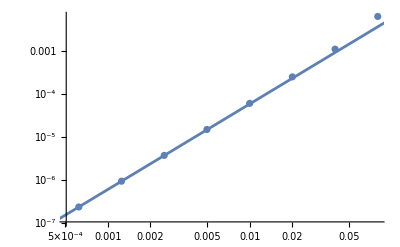

```mathematica
Show[ListLogLogPlot[Table[{listspar[[i]],Abs[1-modesOldpex[[i]]["ω"]/modesNewpex[[i]]["ω"]]},{i,1,Length[listspar]}]],LogLogPlot[(spar/6.25*^-4)^2*2.31*^-7,{spar,0.0001,0.1}]]
```

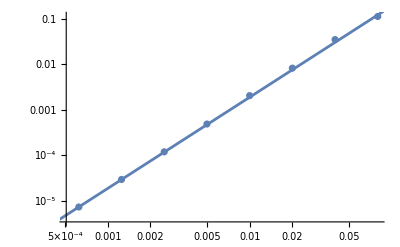

```mathematica
Show[ListLogLogPlot[Table[{listspar[[i]],Abs[1-modesOldpex[[i]]["Amplitudes"]["ℐ"]/modesNewpex[[i]]["Amplitudes"]["ℐ"]]},{i,1,Length[listspar]}]],LogLogPlot[(spar/6.25*^-4)^2*7.4*^-6,{spar,0.0001,0.1}]]
```

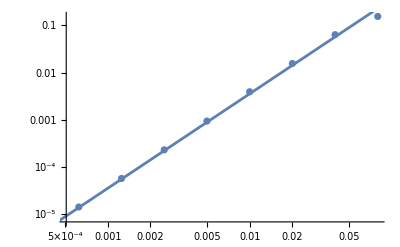

```mathematica
Show[ListLogLogPlot[Table[{listspar[[i]],Abs[1-modesOldpex[[i]]["Fluxes"]["Energy"]["ℐ"]/modespex[[i]]["Fluxes"]["Energy"]["ℐ"]]},{i,1,Length[listspar]}]],LogLogPlot[(spar/6.25*^-4)^2*1.39*^-5,{spar,0.0001,0.1}]]
```

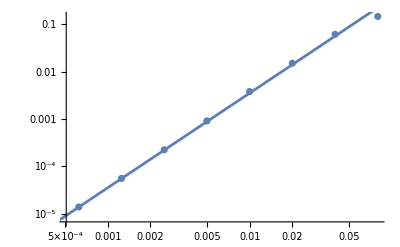

```mathematica
Show[ListLogLogPlot[Table[{listspar[[i]],Abs[1-modesOldpex[[i]]["Fluxes"]["Energy"]["ℐ"]/modesNewpex[[i]]["Fluxes"]["Energy"]["ℐ"]]},{i,1,Length[listspar]}]],LogLogPlot[(spar/6.25*^-4)^2*1.38*^-5,{spar,0.0001,0.1}]]
```

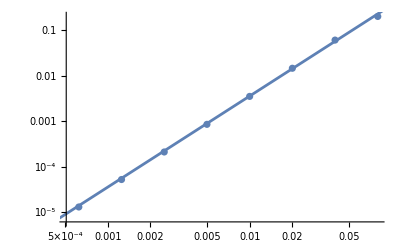

```mathematica
Show[ListLogLogPlot[Table[{listspar[[i]],Abs[1-modesOldpex[[i]]["Fluxes"]["Energy"]["ℋ"]/modesNewpex[[i]]["Fluxes"]["Energy"]["ℋ"]]},{i,1,Length[listspar]}]],LogLogPlot[(spar/6.25*^-4)^2*1.38*^-5,{spar,0.0001,0.1}]]
```

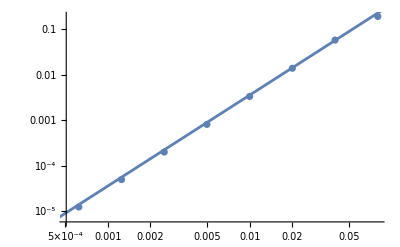

```mathematica
Show[ListLogLogPlot[Table[{listspar[[i]],Abs[1-modesOldpex[[i]]["Fluxes"]["Energy"]["ℋ"]/modespex[[i]]["Fluxes"]["Energy"]["ℋ"]]},{i,1,Length[listspar]}]],LogLogPlot[(spar/6.25*^-4)^2*1.39*^-5,{spar,0.0001,0.1}]]
```

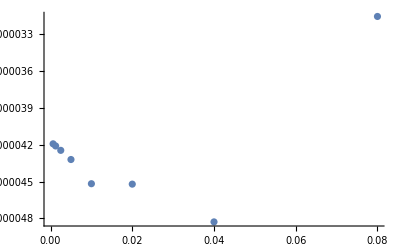

```mathematica
ListPlot[Table[{listspar[[i]],(modesOldpex[[i]]["Fluxes"]["Energy"]["ℐ"]-modesNewpex[[i]]["Fluxes"]["Energy"]["ℐ"])/listspar[[i]]^2},{i,1,Length[listspar]}],PlotRange->All]
```

```mathematica
spar=0.01`48
```

0.01

```mathematica
orbitPlus=KerrSpinOrbit[a,p,e,x,spar]
```

<|a→0.9,p→12.,e→0.2,x→(√3)/2,spar→0.01,Energy→0.96169731977950340076094048662676575728187930428534883594488564,AngularMomentum→3.26946895953061732307367216562517597552783910348238119845524,CarterConstantK→9.35729204317729381252747992024611720194721966562266895078203,EnTilde→0.961820136098200289585674597383336080292357913146946,JzTilde→3.26727174948176193167946806743537760675158451028837,KTilde→9.34909241486853354844181609032271899880989257015879,Frequencies→<|Υ_r→3.1230683911342245129255828270423168855396883,Υ_z→3.78057162518936874776786795827529437935405204,Υ_ϕ→3.9243044749354753903065548825747311994992,Υ_t→174.268061549309056410499999608687547188533|>,BLFrequencies→{0.0179210600230986901366929653320106361353273,0.0216940017096572684013983496140429439588146,0.0225187819273762651107116992908291734323},TrajectoryDeltas→<|Δtr→Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`orbitTilde$10447[TrajectoryDeltas][Δtr][SpinningOrbit`Private`qr$]-(3 0.01 SpinningOrbit`Private`τTilde$10447[ProperTime][0,SpinningOrbit`Private`qr$,0])/(2 SpinningOrbit`Private`sqrtK$10447)],Δtz→Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`orbitTilde$10447[TrajectoryDeltas][Δtθ][SpinningOrbit`Private`qz$]-(3 0.01 SpinningOrbit`Private`τTilde$10447[ProperTime][0,0,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$10447)],Δϕr→Function[{qr$},0.6278169298063490247288299162299415287921964403 (-63.8485431207596780886695545460728609211392 (0.506458383253509039524165155611059292185928 qr$-EllipticPi[0.000132141204609963660423399750794253643678299,JacobiAmplitude[0.50642470584463637555569333589968369040950554 qr$,0.049943944606966369737398926319890409759353406],0.049943944606966369737398926319890409759353406])+1.9984991060446109889322690650078305339252501 (0.51588429840434959979388940449026998290723228 qr$-EllipticPi[0.036110079193835947643710935495779024469733216,JacobiAmplitude[0.50642470584463637555569333589968369040950554 qr$,0.049943944606966369737398926319890409759353406],0.049943944606966369737398926319890409759353406])),Listable],Δϕz→Function[{qθ$},-0.8639525202053686289968349985613008237608974116 (1.15534206684913322378320457833230689702674732 (π/2+qθ$)-EllipticPi[0.25040577700068062490817975951974083988996633661514,JacobiAmplitude[1.00026575484407066579234796510553550890819796 (π/2+qθ$),0.0010623840363541652970290174837532685591803344],0.0010623840363541652970290174837532685591803344]),Listable]|>,Trajectoryg→{Function[{SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},SpinningOrbit`Private`orbitTilde$10447[Trajectory]⟦1⟧[SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]-(3 0.01 SpinningOrbit`Private`τTilde$10447[ProperTime][0,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$10447)],Function[{qr$},(-136.046807081888112304620862751576521319523543+7.6202321096776599207128853680238082052960589 JacobiSN[0.50642470584463637555569333589968369040950554 qr$,0.049943944606966369737398926319890409759353406]^2)/(-13.7510432585361316917867843846194881663633258+5.29627228145174657037104740315134236492675314697 JacobiSN[0.50642470584463637555569333589968369040950554 qr$,0.049943944606966369737398926319890409759353406]^2),Listable],SpinningOrbit`Private`zTilde$10447,Function[{qϕ$,qr$,qθ$},qϕ$+0.6278169298063490247288299162299415287921964403 (-63.8485431207596780886695545460728609211392 (0.506458383253509039524165155611059292185928 qr$-EllipticPi[0.000132141204609963660423399750794253643678299,JacobiAmplitude[0.50642470584463637555569333589968369040950554 qr$,0.049943944606966369737398926319890409759353406],0.049943944606966369737398926319890409759353406])+1.9984991060446109889322690650078305339252501 (0.51588429840434959979388940449026998290723228 qr$-EllipticPi[0.036110079193835947643710935495779024469733216,JacobiAmplitude[0.50642470584463637555569333589968369040950554 qr$,0.049943944606966369737398926319890409759353406],0.049943944606966369737398926319890409759353406]))-0.8639525202053686289968349985613008237608974116 (1.15534206684913322378320457833230689702674732 (π/2+qθ$)-EllipticPi[0.25040577700068062490817975951974083988996633661514,JacobiAmplitude[1.00026575484407066579234796510553550890819796 (π/2+qθ$),0.0010623840363541652970290174837532685591803344],0.0010623840363541652970290174837532685591803344]),Listable]},δx→Function[{SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},{SpinningOrbit`Private`δt3[SpinningOrbit`Private`rTilde$10447[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$10447[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$10447[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$10447[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$10447,0.9],SpinningOrbit`Private`δr3[SpinningOrbit`Private`rTilde$10447[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$10447[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$10447,SpinningOrbit`Private`JzTilde$10447,SpinningOrbit`Private`KTilde$10447,0.9],SpinningOrbit`Private`δz3[SpinningOrbit`Private`rTilde$10447[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$10447[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$10447,SpinningOrbit`Private`JzTilde$10447,SpinningOrbit`Private`KTilde$10447,0.9],SpinningOrbit`Private`δϕ3[SpinningOrbit`Private`rTilde$10447[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$10447[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$10447[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$10447[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$10447,0.9]}],FourVelocitiesg→{Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`UrTilde$10447[SpinningOrbit`Private`qr$]],Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`UzTilde$10447[SpinningOrbit`Private`qz$]]},rootsTilde→{9.893562584601379912140779175529160743625546379482,15.18983486605312648251182657868050310855229952645}|>

```mathematica
orbitMinus=KerrSpinOrbit[a,p,e,x,-spar]
```

<|a→0.9,p→12.,e→0.2,x→0.8,spar→-0.01,Energy→0.96181291429748625538439133098094481922633837037195159298579579,AngularMomentum→3.03161436070341245886292657730611059741395637677064636256094,CarterConstantK→9.88308737027204536842554533587846408566536767270694660904733,EnTilde→0.961693763269952633158428785173748502450124562806276,JzTilde→3.03338907270776683002583725764603843229432660580259,KTilde→9.8947216982713566331132483292988095053566937620368,Frequencies→<|Υ_r→3.1127652149463022198896635184382177522694716,Υ_z→3.7977581541563137792152123366667473665618514,Υ_ϕ→3.9430886914397966307941644346059928277,Υ_t→174.614675345252097397457052207127791235|>,BLFrequencies→{0.0178264811293304656139132144440815803766,0.0217493641164312232116592847506663914028,0.022581656917687085677380225471972502114},TrajectoryDeltas→<|Δtr→Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`orbitTilde$20377[TrajectoryDeltas][Δtr][SpinningOrbit`Private`qr$]-(3 (-0.01) SpinningOrbit`Private`τTilde$20377[ProperTime][0,SpinningOrbit`Private`qr$,0])/(2 SpinningOrbit`Private`sqrtK$20377)],Δtz→Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`orbitTilde$20377[TrajectoryDeltas][Δtθ][SpinningOrbit`Private`qz$]-(3 (-0.01) SpinningOrbit`Private`τTilde$20377[ProperTime][0,0,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$20377)],Δϕr→Function[{qr$},0.631134403059487932797776859580157626644604616 (334.3134345819735813581709270599445668204 (0.5053648219744798061342943653422290477751 qr$-EllipticPi[4.011285873312696114038816996275501576864×10^-6,JacobiAmplitude[0.5053638029700074634984391547001840601575738 qr$,0.041893523689596157701449513739490852372701395],0.041893523689596157701449513739490852372701395])+1.7826242885219752968250157794458552951351905 (0.51370952451445877487831358428509191543888326 qr$-EllipticPi[0.032059349332205769407003822931452209179247346,JacobiAmplitude[0.5053638029700074634984391547001840601575738 qr$,0.041893523689596157701449513739490852372701395],0.041893523689596157701449513739490852372701395])),Listable],Δϕz→Function[{qθ$},-0.7983845234810707803290950609713312122455343147 (1.25041288359122654468761050689606817694445853 (π/2+qθ$)-EllipticPi[0.35988276755197186096843734324735786585773256582203,JacobiAmplitude[1.00037973214797111033215308312931776352224417 (π/2+qθ$),0.00151763167158478520626943475801593659821604219],0.00151763167158478520626943475801593659821604219]),Listable]|>,Trajectoryg→{Function[{SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},SpinningOrbit`Private`orbitTilde$20377[Trajectory]⟦1⟧[SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]-(3 (-0.01) SpinningOrbit`Private`τTilde$20377[ProperTime][0,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$20377)],Function[{qr$},(-135.20335506560960675135108475511451745553206+6.740745376627317399334652240651449915909535 JacobiSN[0.5053638029700074634984391547001840601575738 qr$,0.041893523689596157701449513739490852372701395]^2)/(-13.3703425590424824031175658702984864271291658+4.69414825875650483680015301985030351955814477059 JacobiSN[0.5053638029700074634984391547001840601575738 qr$,0.041893523689596157701449513739490852372701395]^2),Listable],SpinningOrbit`Private`zTilde$20377,Function[{qϕ$,qr$,qθ$},qϕ$+0.631134403059487932797776859580157626644604616 (334.3134345819735813581709270599445668204 (0.5053648219744798061342943653422290477751 qr$-EllipticPi[4.011285873312696114038816996275501576864×10^-6,JacobiAmplitude[0.5053638029700074634984391547001840601575738 qr$,0.041893523689596157701449513739490852372701395],0.041893523689596157701449513739490852372701395])+1.7826242885219752968250157794458552951351905 (0.51370952451445877487831358428509191543888326 qr$-EllipticPi[0.032059349332205769407003822931452209179247346,JacobiAmplitude[0.5053638029700074634984391547001840601575738 qr$,0.041893523689596157701449513739490852372701395],0.041893523689596157701449513739490852372701395]))-0.7983845234810707803290950609713312122455343147 (1.25041288359122654468761050689606817694445853 (π/2+qθ$)-EllipticPi[0.35988276755197186096843734324735786585773256582203,JacobiAmplitude[1.00037973214797111033215308312931776352224417 (π/2+qθ$),0.00151763167158478520626943475801593659821604219],0.00151763167158478520626943475801593659821604219]),Listable]},δx→Function[{SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},{SpinningOrbit`Private`δt3[SpinningOrbit`Private`rTilde$20377[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$20377[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$20377[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$20377[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$20377,0.9],SpinningOrbit`Private`δr3[SpinningOrbit`Private`rTilde$20377[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$20377[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$20377,SpinningOrbit`Private`JzTilde$20377,SpinningOrbit`Private`KTilde$20377,0.9],SpinningOrbit`Private`δz3[SpinningOrbit`Private`rTilde$20377[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$20377[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$20377,SpinningOrbit`Private`JzTilde$20377,SpinningOrbit`Private`KTilde$20377,0.9],SpinningOrbit`Private`δϕ3[SpinningOrbit`Private`rTilde$20377[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$20377[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$20377[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$20377[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$20377,0.9]}],FourVelocitiesg→{Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`UrTilde$20377[SpinningOrbit`Private`qr$]],Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`UzTilde$20377[SpinningOrbit`Private`qz$]]},rootsTilde→{10.11218332429114667554643174491111506560328918118,14.80633158304765151234658476476141858516143395178}|>

```mathematica
l=2
m=2
n=1
k=1
```

2

2

1

1

```mathematica
modePlus=TeukolskySpinModeFromCorrectionAnalytical[l,m,n,k,orbitPlus]
```

64 steps in wr, 32 steps in wz

<|l→2,m→2,k→1,n→1,ω→0.084652625587508488759514713527711926958734,Amplitudes→<|ℐ→-9.114420725335034004329762727993484×10^-7-2.4799458041675364203737490435674458×10^-6 ⅈ,ℋ→7.89597604964850101812838447266522724×10^-6-0.00002720793992122840069506828442587735263 ⅈ|>,α→-0.004276283698757314868944579531002089264482,S→0.1523647125472603041639332108459698794151,Fluxes→<|Energy→<|ℐ→7.752076765692919653540287385439384×10^-11,ℋ→-3.81140333294969485724361791752741869×10^-11|>,AngularMomentum→<|ℐ→1.831502971559769706977958341688668×10^-9,ℋ→-9.00480831279050883575147575874288101×10^-10|>|>,stepsr→64,stepsz→32|>

```mathematica
modeMinus=TeukolskySpinModeFromCorrectionAnalytical[l,m,n,k,orbitMinus]
```

48 steps in wr, 32 steps in wθ

<|l→2,m→2,k→1,n→1,ω→0.084739159081135860180332950138692976007,Amplitudes→<|ℐ→-1.0502169401238693496698766501997×10^-6-2.66658042234583525093005634905429×10^-6 ⅈ,ℋ→8.483767137502434388702496348027177×10^-6-0.000029034805279882363021785478348940398 ⅈ|>,α→-0.0042872947479795468128582803926948647007,S→0.1523592738145807687333194300469553275,Fluxes→<|Energy→<|ℐ→9.1023963680317325448308073176802×10^-11,ℋ→-4.347339226746015204728913861250253×10^-11|>,AngularMomentum→<|ℐ→2.1483329470655686974979482091455×10^-9,ℋ→-1.026052010401362275036312525086103×10^-9|>|>,stepsr→48,stepsz→32|>

```mathematica
(modePlus-modeMinus)/(2*spar)
```

<|l→0,m→0,k→0,n→0,ω→0.0026125175327066280950216950997229668,Amplitudes→<|ℐ→6.014087817545105373559936601015×10^-6-3.196297084538485762230967701611×10^-6 ⅈ,ℋ→0.0000190626452070773630070335753326133-0.0000846057593088242383035195346913214 ⅈ|>,α→-0.00033278416220501472524464933505536949,S→-0.000164199197173141662290680578188132,Fluxes→<|Energy→<|ℐ→5.35189534616294723097235899701×10^-11,ℋ→-2.56717183400164199614738804692792×10^-10|>,AngularMomentum→<|ℐ→1.19617482611313283566256330836×10^-9,ℋ→-6.02365017112446018063192225849574×10^-9|>|>,stepsr→800.,stepsz→0|>

```mathematica
spar
```

0.01

```mathematica
orbitPlus=KerrSpinOrbit[a,p,e,x,spar]
```

<|a→0.9,p→12.,e→0.2,x→(√3)/2,spar→0.01,Energy→0.96169731977950340076094048662676575728187930428534883594488564,AngularMomentum→3.26946895953061732307367216562517597552783910348238119845524,CarterConstantK→9.35729204317729381252747992024611720194721966562266895078203,EnTilde→0.961820136098200289585674597383336080292357913146946,JzTilde→3.26727174948176193167946806743537760675158451028837,KTilde→9.34909241486853354844181609032271899880989257015879,Frequencies→<|Υ_r→3.1230683911342245129255828270423168855396883,Υ_z→3.78057162518936874776786795827529437935405204,Υ_ϕ→3.9243044749354753903065548825747311994992,Υ_t→175.019934608347727783092406880671461492938|>,BLFrequencies→{0.0178440724373648980535996522145821208209922,0.0216008058376285732010547286985602348825743,0.02242204285881559391338231737490021302606},TrajectoryDeltas→<|Δtr→Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`orbitTilde$424919[TrajectoryDeltas][Δtr][SpinningOrbit`Private`qr$]-(0 3 0.01 SpinningOrbit`Private`τTilde$424919[ProperTime][0,SpinningOrbit`Private`qr$,0])/(2 SpinningOrbit`Private`sqrtK$424919)],Δtz→Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`orbitTilde$424919[TrajectoryDeltas][Δtθ][SpinningOrbit`Private`qz$]-(0 3 0.01 SpinningOrbit`Private`τTilde$424919[ProperTime][0,0,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$424919)],Δϕr→Function[{qr$},0.6278169298063490247288299162299415287921964403 (-63.8485431207596780886695545460728609211392 (0.506458383253509039524165155611059292185928 qr$-EllipticPi[0.000132141204609963660423399750794253643678299,JacobiAmplitude[0.50642470584463637555569333589968369040950554 qr$,0.049943944606966369737398926319890409759353406],0.049943944606966369737398926319890409759353406])+1.9984991060446109889322690650078305339252501 (0.51588429840434959979388940449026998290723228 qr$-EllipticPi[0.036110079193835947643710935495779024469733216,JacobiAmplitude[0.50642470584463637555569333589968369040950554 qr$,0.049943944606966369737398926319890409759353406],0.049943944606966369737398926319890409759353406])),Listable],Δϕz→Function[{qθ$},-0.8639525202053686289968349985613008237608974116 (1.15534206684913322378320457833230689702674732 (π/2+qθ$)-EllipticPi[0.25040577700068062490817975951974083988996633661514,JacobiAmplitude[1.00026575484407066579234796510553550890819796 (π/2+qθ$),0.0010623840363541652970290174837532685591803344],0.0010623840363541652970290174837532685591803344]),Listable]|>,Trajectoryg→{Function[{SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},SpinningOrbit`Private`orbitTilde$424919[Trajectory]⟦1⟧[SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]-(3 0.01 SpinningOrbit`Private`τTilde$424919[ProperTime][0,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$424919)],Function[{qr$},(-136.046807081888112304620862751576521319523543+7.6202321096776599207128853680238082052960589 JacobiSN[0.50642470584463637555569333589968369040950554 qr$,0.049943944606966369737398926319890409759353406]^2)/(-13.7510432585361316917867843846194881663633258+5.29627228145174657037104740315134236492675314697 JacobiSN[0.50642470584463637555569333589968369040950554 qr$,0.049943944606966369737398926319890409759353406]^2),Listable],SpinningOrbit`Private`zTilde$424919,Function[{qϕ$,qr$,qθ$},qϕ$+0.6278169298063490247288299162299415287921964403 (-63.8485431207596780886695545460728609211392 (0.506458383253509039524165155611059292185928 qr$-EllipticPi[0.000132141204609963660423399750794253643678299,JacobiAmplitude[0.50642470584463637555569333589968369040950554 qr$,0.049943944606966369737398926319890409759353406],0.049943944606966369737398926319890409759353406])+1.9984991060446109889322690650078305339252501 (0.51588429840434959979388940449026998290723228 qr$-EllipticPi[0.036110079193835947643710935495779024469733216,JacobiAmplitude[0.50642470584463637555569333589968369040950554 qr$,0.049943944606966369737398926319890409759353406],0.049943944606966369737398926319890409759353406]))-0.8639525202053686289968349985613008237608974116 (1.15534206684913322378320457833230689702674732 (π/2+qθ$)-EllipticPi[0.25040577700068062490817975951974083988996633661514,JacobiAmplitude[1.00026575484407066579234796510553550890819796 (π/2+qθ$),0.0010623840363541652970290174837532685591803344],0.0010623840363541652970290174837532685591803344]),Listable]},δx→Function[{SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},{SpinningOrbit`Private`δt3[SpinningOrbit`Private`rTilde$424919[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$424919[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$424919[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$424919[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$424919,0.9],SpinningOrbit`Private`δr3[SpinningOrbit`Private`rTilde$424919[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$424919[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$424919,SpinningOrbit`Private`JzTilde$424919,SpinningOrbit`Private`KTilde$424919,0.9],SpinningOrbit`Private`δz3[SpinningOrbit`Private`rTilde$424919[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$424919[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$424919,SpinningOrbit`Private`JzTilde$424919,SpinningOrbit`Private`KTilde$424919,0.9],SpinningOrbit`Private`δϕ3[SpinningOrbit`Private`rTilde$424919[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$424919[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$424919[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$424919[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$424919,0.9]}],FourVelocitiesg→{Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`UrTilde$424919[SpinningOrbit`Private`qr$]],Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`UzTilde$424919[SpinningOrbit`Private`qz$]]},rootsTilde→{9.893562584601379912140779175529160743625546379482,15.18983486605312648251182657868050310855229952645}|>

```mathematica
orbitMinus=KerrSpinOrbit[a,p,e,x,-spar]
```

<|a→0.9,p→12.,e→0.2,x→(√3)/2,spar→-0.01,Energy→0.96169731977950340076094048662676575728187930428534883594488564,AngularMomentum→3.26946895953061732307367216562517597552783910348238119845524,CarterConstantK→9.35729204317729381252747992024611720194721966562266895078203,EnTilde→0.961574503460806511936206375870195434271400695423752,JzTilde→3.27166616957947271446787626381497434430409369667639,KTilde→9.36549167148605407661314375016951540508454676108655,Frequencies→<|Υ_r→3.1274131583870963183200801180687017155387076,Υ_z→3.78364492736120297825077836666044714753098549,Υ_ϕ→3.9267668810139216811381013566302371524532,Υ_t→173.760882197138352320706753000535646259133|>,BLFrequencies→{0.0179983729297536987323465844428400196214877,0.021775009884379577492459351125800425091625,0.02259868177095725603068472331674106709169},TrajectoryDeltas→<|Δtr→Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`orbitTilde$424981[TrajectoryDeltas][Δtr][SpinningOrbit`Private`qr$]-(0 3 (-0.01) SpinningOrbit`Private`τTilde$424981[ProperTime][0,SpinningOrbit`Private`qr$,0])/(2 SpinningOrbit`Private`sqrtK$424981)],Δtz→Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`orbitTilde$424981[TrajectoryDeltas][Δtθ][SpinningOrbit`Private`qz$]-(0 3 (-0.01) SpinningOrbit`Private`τTilde$424981[ProperTime][0,0,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$424981)],Δϕr→Function[{qr$},0.6276482070119253120006994867917757361973739213 (-62.4694232203846501864832252903885866434273 (0.505759322406109385040358676675706766339252 qr$-EllipticPi[0.000123502518826179510337024660848293274386691,JacobiAmplitude[0.50572791178900599032579175134862023975739412 qr$,0.044665082085574878787330047045112024455183917],0.044665082085574878787330047045112024455183917])+2.0078330061285138272009089309951182951405473 (0.51413374993590771885382865593577882529248496 qr$-EllipticPi[0.032250546267001437158630755888862730480889787,JacobiAmplitude[0.50572791178900599032579175134862023975739412 qr$,0.044665082085574878787330047045112024455183917],0.044665082085574878787330047045112024455183917])),Listable],Δϕz→Function[{qθ$},-0.8644112816742176905837665910273057171588779808 (1.15471779127788838823423509199088076054199048 (π/2+qθ$)-EllipticPi[0.24959455204228593632393249743444518662282323690658,JacobiAmplitude[1.00026613188804436782789457747458612074728417 (π/2+qθ$),0.00106389040858613917679132900901451183119370025],0.00106389040858613917679132900901451183119370025]),Listable]|>,Trajectoryg→{Function[{SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},SpinningOrbit`Private`orbitTilde$424981[Trajectory]⟦1⟧[SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]-(3 (-0.01) SpinningOrbit`Private`τTilde$424981[ProperTime][0,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$424981)],Function[{qr$},(-135.13551120002366647024534198353451690733869+6.7683534719679323767386895026081971025589031 JacobiSN[0.50572791178900599032579175134862023975739412 qr$,0.044665082085574878787330047045112024455183917]^2)/(-13.3712311911341930689677630606958314382190866+4.70372771854825342962895259684865763507324685303 JacobiSN[0.50572791178900599032579175134862023975739412 qr$,0.044665082085574878787330047045112024455183917]^2),Listable],SpinningOrbit`Private`zTilde$424981,Function[{qϕ$,qr$,qθ$},qϕ$+0.6276482070119253120006994867917757361973739213 (-62.4694232203846501864832252903885866434273 (0.505759322406109385040358676675706766339252 qr$-EllipticPi[0.000123502518826179510337024660848293274386691,JacobiAmplitude[0.50572791178900599032579175134862023975739412 qr$,0.044665082085574878787330047045112024455183917],0.044665082085574878787330047045112024455183917])+2.0078330061285138272009089309951182951405473 (0.51413374993590771885382865593577882529248496 qr$-EllipticPi[0.032250546267001437158630755888862730480889787,JacobiAmplitude[0.50572791178900599032579175134862023975739412 qr$,0.044665082085574878787330047045112024455183917],0.044665082085574878787330047045112024455183917]))-0.8644112816742176905837665910273057171588779808 (1.15471779127788838823423509199088076054199048 (π/2+qθ$)-EllipticPi[0.24959455204228593632393249743444518662282323690658,JacobiAmplitude[1.00026613188804436782789457747458612074728417 (π/2+qθ$),0.00106389040858613917679132900901451183119370025],0.00106389040858613917679132900901451183119370025]),Listable]},δx→Function[{SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},{SpinningOrbit`Private`δt3[SpinningOrbit`Private`rTilde$424981[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$424981[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$424981[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$424981[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$424981,0.9],SpinningOrbit`Private`δr3[SpinningOrbit`Private`rTilde$424981[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$424981[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$424981,SpinningOrbit`Private`JzTilde$424981,SpinningOrbit`Private`KTilde$424981,0.9],SpinningOrbit`Private`δz3[SpinningOrbit`Private`rTilde$424981[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$424981[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$424981,SpinningOrbit`Private`JzTilde$424981,SpinningOrbit`Private`KTilde$424981,0.9],SpinningOrbit`Private`δϕ3[SpinningOrbit`Private`rTilde$424981[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$424981[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$424981[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$424981[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$424981,0.9]}],FourVelocitiesg→{Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`UrTilde$424981[SpinningOrbit`Private`qr$]],Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`UzTilde$424981[SpinningOrbit`Private`qz$]]},rootsTilde→{10.10643741539862008785922082447083925637445362052,14.81016513394687351748817342131949689144770047355}|>

```mathematica
orbit0=KerrSpinOrbit[a,p,e,x,0];
```

```mathematica
mode0=TeukolskySpinModeFromCorrectionAnalytical[l,m,n,k,orbit0]
```

64 steps in wr, 32 steps in wz

<|l→2,m→2,k→1,n→1,ω→0.0846269293219830827014134346489077203292882577237889457,Amplitudes→<|ℐ→-8.89269064668737030721192879261039503472232600108×10^-7-2.425774722125796256682391077727335809306496236714×10^-6 ⅈ,ℋ→7.7305773861351128935675428474279539615571528882442×10^-6-0.000026648509532844730087464886480819304018811526295836 ⅈ|>,α→-0.00427301674590237256836094349791446973255889685719173393,S→0.152366327593006852309126205181740180035718947623291962,Fluxes→<|Energy→<|ℐ→7.41713378053047886195893495704714744061530304224×10^-11,ℋ→-3.6554819305640493512785308179483658952737763787113×10^-11|>,AngularMomentum→<|ℐ→1.75290155035880992895963618535360160385289725074×10^-9,ℋ→-8.6390513276356925603176198912875321876452400291535×10^-10|>|>,stepsr→64,stepsz→32|>

```mathematica
modePlus=TeukolskySpinModeFromCorrectionAnalytical[l,m,n,k,orbitPlus]
```

64 steps in wr, 32 steps in wz

<|l→2,m→2,k→1,n→1,ω→0.084288963992624659081419015662942781755677,Amplitudes→<|ℐ→-9.746652266061750667897263893066617×10^-7-2.4815476247232477278641701987407763×10^-6 ⅈ,ℋ→7.87198861621149752031922571683036384×10^-6-0.00002699627429179917674595494207092288141 ⅈ|>,α→-0.004230168033738124750328824866448206074337,S→0.1523875693927898970234739640749366968515,Fluxes→<|Energy→<|ℐ→7.961579468113767457797742133282638×10^-11,ℋ→-3.74675139053839827823530675622074243×10^-11|>,AngularMomentum→<|ℐ→1.889115511921681942738753875686904×10^-9,ℋ→-8.89025374867875120515492077497969911×10^-10|>|>,stepsr→64,stepsz→32|>

```mathematica
modeMinus=TeukolskySpinModeFromCorrectionAnalytical[l,m,n,k,orbitMinus]
```

48 steps in wr, 32 steps in wz

<|l→2,m→2,k→1,n→1,ω→0.084970746356047788286175382202122578896483,Amplitudes→<|ℐ→-8.09386917998968594122429277429247×10^-7-2.3711179734497562364341695827869002×10^-6 ⅈ,ℋ→7.5536949575349096882449495021455801×10^-6-0.00002616458213651193371561656681801914395 ⅈ|>,α→-0.00431683472654296138805344582252551873449,S→0.1523447184072949340214884208697672765043,Fluxes→<|Energy→<|ℐ→6.918702909748244128479257675295836×10^-11,ℋ→-3.5286776248014405807483032338477477×10^-11|>,AngularMomentum→<|ℐ→1.628490558564054750654243934906317×10^-9,ℋ→-8.30562935157809671572776762213649052×10^-10|>|>,stepsr→48,stepsz→32|>

```mathematica
(modePlus-modeMinus)/(2*spar)
```

<|l→0,m→0,k→0,n→0,ω→-0.03408911817115646023781832695898985704,Amplitudes→<|ℐ→-8.26391543036032363336485559387073×10^-6-5.5214825636745745715000307976938×10^-6 ⅈ,ℋ→0.00001591468293382939160371381073423919-0.000041584607764362151516918762645186873 ⅈ|>,α→0.0043333346402418318862310478038656330076,S→0.00214254927474815009927716025847101736,Fluxes→<|Energy→<|ℐ→5.21438279182761664659242228993401×10^-10,ℋ→-1.0903688286847884874350176118649737×10^-10|>,AngularMomentum→<|ℐ→1.30312476678813596042254970390294×10^-8,ℋ→-2.923121985503272447135765764216043×10^-9|>|>,stepsr→800.,stepsz→0|>

```mathematica
(%322["Amplitudes"]-%314["Amplitudes"])/mode0["Amplitudes"]
```

<|ℐ→0.93700096553238193667505821378275-2.28254089740065521898246940305894 ⅈ,ℋ→-0.7383244754164404863299964516994846+0.129206459536015825812978711757462 ⅈ|>

```mathematica
(%322["Fluxes"]-%314["Fluxes"])/mode0["Fluxes"]
```

<|Energy→<|ℐ→2.7401937432065025690852842129938,ℋ→-1.694732327583702287997111032641056|>,AngularMomentum→<|ℐ→3.1709379837089081587385941636205,ℋ→-1.267263112566085185281434544196822|>|>

```mathematica
3*orbit0["Energy"]/2/Sqrt[orbit0["CarterConstantK"]]
```

0.458918479251799282449930200335658085960876892637656249547996

## Trajectory

```mathematica
spar=0.01`64
```

0.01

```mathematica
orbit=KerrSpinOrbit[a,p,e,x,spar];
```

```mathematica
orbit["EnTilde"]
```

0.96193206532501987761035387678814113600255217793762678028932177

```mathematica
orbit["TrajectoryDeltas"]["Δtr"][0.3`48]
```

-5.5001189855621301979833054228455586711238547

```mathematica
orbit["Trajectoryg"][[1]][0.1,0.2,0.3]
```

-3.57508

```mathematica
orbit["Trajectoryg"][[4]][2Pi,0.2,0.3]
```

6.35421

```mathematica
orbit["δx"][0.2,0.3]
```

{0.040103,2.96701,0.00407446,0.00202126}

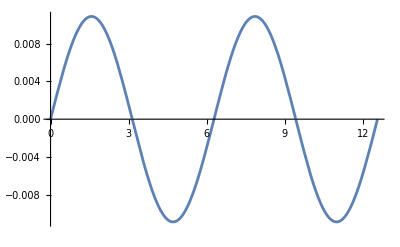

```mathematica
Plot[orbit["TrajectoryDeltas"]["Δϕr"][qr],{qr,0,4Pi}]
```

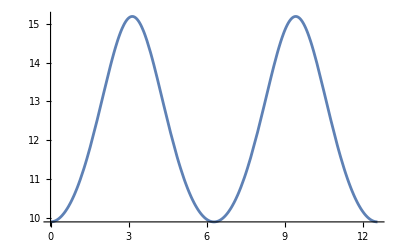

```mathematica
Plot[orbit["Trajectoryg"][[2]][qr],{qr,0,4Pi}]
```

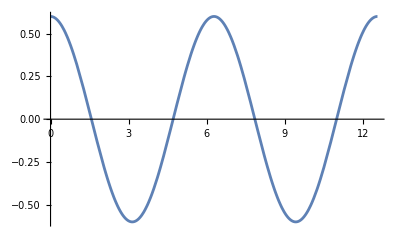

```mathematica
Plot[orbit["Trajectoryg"][[3]][qz],{qz,0,4Pi}]
```

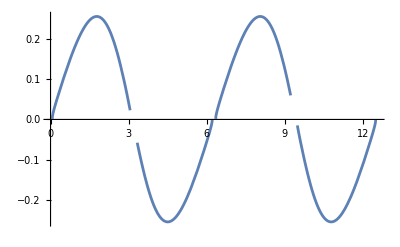

```mathematica
Plot[orbit["δx"][qr,0.3][[1]],{qr,0,4Pi}]
```

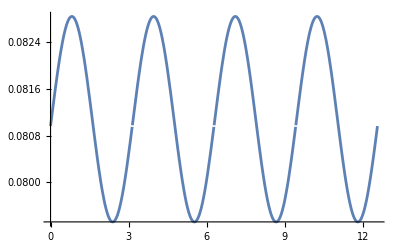

```mathematica
Plot[orbit["δx"][0.4,qz][[1]],{qz,0,4Pi}]
```

```mathematica
Plot3D[orbit["δx"][qr,qz][[2]],{qr,0,4Pi},{qz,0,4Pi}]
```

-Graphics3D-

```mathematica
Plot3D[orbit["δx"][qr,qz][[3]],{qr,0,4Pi},{qz,0,4Pi}]
```

-Graphics3D-

```mathematica
Plot3D[orbit["δx"][qr,qz][[4]],{qr,0,4Pi},{qz,0,4Pi}]
```

-Graphics3D-